## Common elements

References:
[MSc] F.Hekhorn, “Sub-leading Terms in Heavy Quark Soft Gluon Resummation”, MSc Thesis Universität Tübingen, Germany, 2015.
[Bonc] R. Bonciani, S. Catani, M. L. Mangano, and P. Nason, “NLL resummation of the heavy quark hadroproduction cross-section,” Nucl.Phys. B529 (1998) 424–450, arXiv:hep-ph/9801375 [hep-ph].
[InvMelTh] https://en.wikipedia.org/wiki/Mellin_inversion_theorem
[MP] S. Catani, M. L. Mangano, P. Nason, and L. Trentadue, “The resummation of soft gluons in hadronic collisions,” Nuclear Physics B 478 no. 1–2, (1996) 273 – 310.

```mathematica
(* load packages *)
AppendTo[$Path, ToFileName[{$HomeDirectory,"Physik/PhD/MMa"}]];
Get["MellinTrafoLogCoeffs.m"]
Get["SudakovFactor.m"]
Get["NumericMellinTrafo.m"]
Needs["HEPMath`LHAPDF`"]
(*Get["PdfUtils.m"]*)
Get["zPlot.m"]
Needs["PlotLegends`"]
```

ν::shdw: Symbol "\[Nu]" appears in multiple contexts {"SudakovFactor`", "Global`"}; definitions in context "SudakovFactor`" may shadow or be shadowed by other definitions.

```mathematica
(* give concrete parameters *)
CFCASub = {CF -> 4/3, CA -> 3};
(* @param mQ override default mass *)
(* @param αμ override default running coupling from PDF *)
Options[toN] = {"channel" -> "γg","Q" -> "c","pdfParams"-> {"cteq66",0}, "mQ"-> -1, "αμ"-> -1};
toN[opts:OptionsPattern[]] := Module[{Q,ch,cαμ,r,l,p},
Q=OptionValue["Q"];
ch=OptionValue["channel"];
r=SudakovFactor`getRules[ch];
(* params related to quark *)
l = {
nl-> Switch[Q,"t",5,"b",4,"c",3,_,Throw["unknown quark"]] ,(* number light flaours *)
eQ-> Switch[Q,"t",2/3,"b",-1/3,"c",2/3,_,Throw["unknown quark"]] ,(* electric charge *)
mQ-> If[OptionValue["mQ"] >0,OptionValue["mQ"],Switch[Q,"t",173.070,"b",4.180,"c",1.5(*1.275*),_,Throw["unknown quark"]]], (* [GeV] *)
μ-> mQ (* [GeV] *)
};
(* params related to PDF *)
cαμ=OptionValue["αμ"];
p={αμ-> If[NumericQ[cαμ]&& cαμ≤ 0,
Evaluate@Module[{pdfId,α},
pdfId=LHAPDFOpen@@OptionValue["pdfParams"];
α=LHAPDFAlphaS[pdfId,μ//.l];
LHAPDFClose[pdfId];
α
],
cαμ]};
(* join all *)
Join[r,CFCASub,l,p,{lnRScale4->lnScale4,lnFScale4 ->lnScale4,lnScale4-> Log[μ^2/(4*mQ^2)]}]
];
nLandau =Exp[1/(2αμ*b0)];
```

```mathematica
(* transformations *)
ρ2β[ρ_]=Sqrt[1-ρ];
β2ρ[β_]=1-β^2;
ρ2η[ρ_]=1/ρ-1;
η2ρ[η_] = 1/(1+η);
β2χ[β_]=(1-β)/(1+β);
χ2β[χ_]=(1-χ)/(1+χ);
s2ρ[s_]=4*mQ/s;
vars2ρ[e_] :=e//. {β->ρ2β@ρ,η->ρ2η@ρ,χ->β2χ@ρ2β@ρ};
```

```mathematica
(* build resummation factor *)
ΔLL = Exp[lnN * getG[1][αμ*b0*lnN]];
```

```mathematica
(* used colors *)
Table[Graphics[{c,Disk[]},ImageSize-> 50],{c,ColorData[3,"ColorList"]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Born cross section

```mathematica
(* Born cross sections of unpol. photoproduction *)
Born = π/4 ρ(-(3-β^4)Log[χ]+2β^3-4β);
Module[{a,mlnχ},
a = {0.9991,−0.4828,0.2477,−0.0712};
mlnχ[u_,v_]=n↦Beta[n+u,v/2+1](PolyGamma[n+u+v/2+1]-PolyGamma[n+u])+2*Sum[a[[j]]*Beta[n+u,(v+j)/2+1],{j,Length@a}];
BornN = n↦Evaluate[π/4*(-4Beta[n+1,3/2]+2Beta[n+1,5/2]+3*mlnχ[1,0][n]-mlnχ[1,4][n])];
]
```

```mathematica
(* deduce series of Born in β *)
(*Series[-Log[β2χ@β],{β,0,11}]
Table[2(1/(2k-1)),{k,6}]
Series[-(3-β^4)Log[β2χ@β],{β,0,11}]
{6,2}~Join~Table[2(3/(2k-1)-1/(2k-5)),{k,3,6}]
{2,2,-4-4/5}~Join~Table[2(3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7)),{k,4,8}]*)
BornβSerCoeff[1] =1;
BornβSerCoeff[2] =1;
BornβSerCoeff[3] =-12/5;
BornβSerCoeff[k_Integer] := (3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7))/;k>3;
(* check *)
Series[2/π*(vars2ρ@Born/.{ρ-> β2ρ@β}),{β,0,21}]
Table[BornβSerCoeff@k,{k,11}]
(* the coefficients sum up to 0 *)
(* maybe this results hold more generally for all kind of partonic Born cross sections? at least it does for hadro-quark *)
BornβSerCoeff[1]+BornβSerCoeff[2]+BornβSerCoeff[3]+Sum[(3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7)),{k,4,∞}]
(* numeric check *)
Table[N@Total[CoefficientList[Normal@Series[(Born//.{χ-> β2χ@β,ρ-> β2ρ@β}),{β,0,2*k-1}],β]],{k,{1,2,3,5,10,20,50,100,1000}}]
```

β+β^3-(12 β^5)/5+(52 β^7)/105+(4 β^9)/105-(4 β^11)/1155-(92 β^13)/9009-(68 β^15)/6435-(116 β^17)/12155-(524 β^19)/62985-(244 β^21)/33915+O[β]^22

{1,1,-12/5,52/105,4/105,-4/1155,-92/9009,-68/6435,-116/12155,-524/62985,-244/33915}

0

{1.5708,3.14159,-0.628319,0.20944,0.143301,0.0759506,0.0310652,0.015625,0.00157001}

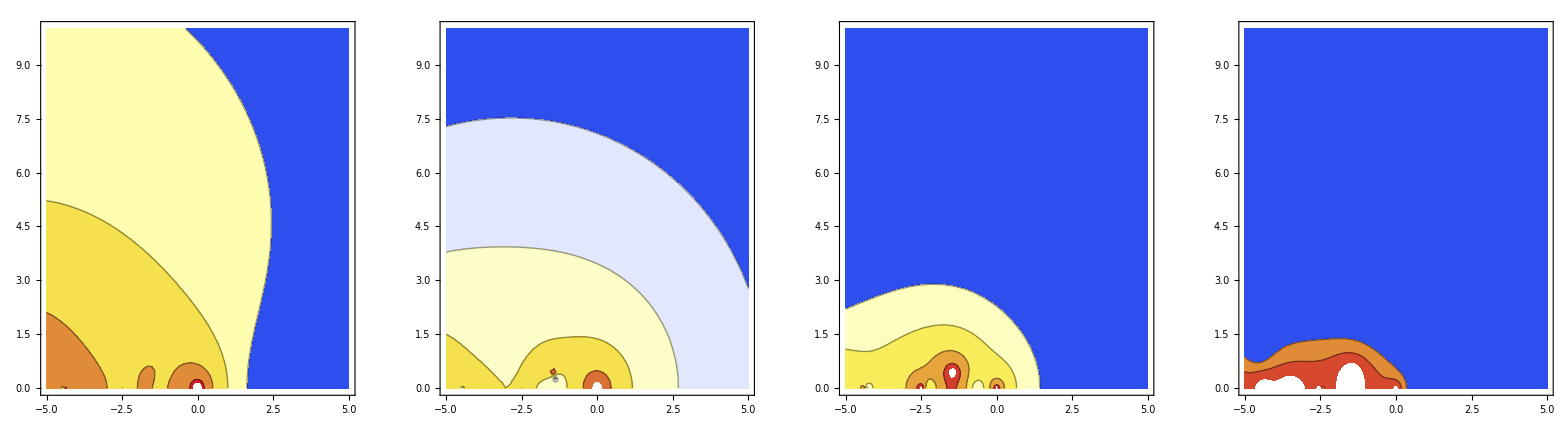

```mathematica
(* check convergence in N-space: *)
Module[{orders,BornMaxSer,BornSers,BornSerβList,BornSerNs,m},
orders = {1,3,5,9};
(* compute series *)
BornMaxSer=Normal@Series[(Born//.{χ-> β2χ@β,ρ-> β2ρ@β}),{β,0,Max@orders}];
BornSers = Table[Normal@Series[BornMaxSer,{β,0,v}],{v,orders}];
(* transform to N *)
BornSerβList=(s↦CoefficientList[s,β])/@BornSers;
BornSerNs=(l↦(n↦Evaluate[l//.{m-> n}]))/@((l↦Total[MapIndexed[Function[{c,ind},c*Beta[m,(First@ind-1)/2+1]],l]])/@BornSerβList);
GraphicsRow[(f↦ContourPlot[Log[Abs[(BornN[n]-f[n])/BornN[n]]//.{n-> re + I im}],{re,-5,5},{im,0,10},ColorFunction->"TemperatureMap",Contours-> {-2,-1,0,1,2,3}])/@BornSerNs]
]
```

## Compare re-expansion to full resummation

Question (Q): how does the reexpanion of the Sudakov-exponent behave? Reexpansion refers to the exponent (i.e. exp ~ 1+O(lnN)). Does it converge in (any sense) to the full resummation?
Conjecture (C): No. Long Answer see [MSc]: “This is probably the reason why the re-expansion of the resummed expression does not converge to the fully resummed expression because near threshold the region N → ∞ is relevant, but it is obviously not in the region of convergence. So how is it possible to match the re-expansion and fixed-order calculations as said above in section 3.2.1? It is probably possible because they rely on the same assumption: α_s (μ.b2) is a small number. If α s is not a good expansion parameter (as it did not catch the relevant region), is there any other? Unfortunately not, because there is always a structure with ln ln x, that limits the convergence.” Can we precise this statement any further?

As a first step I always use the “threshold-resummation”, i.e. I use only a single Beta-function in resummation and NOT the full Born cross section. In a second step, I look on what would change by taking the full Born

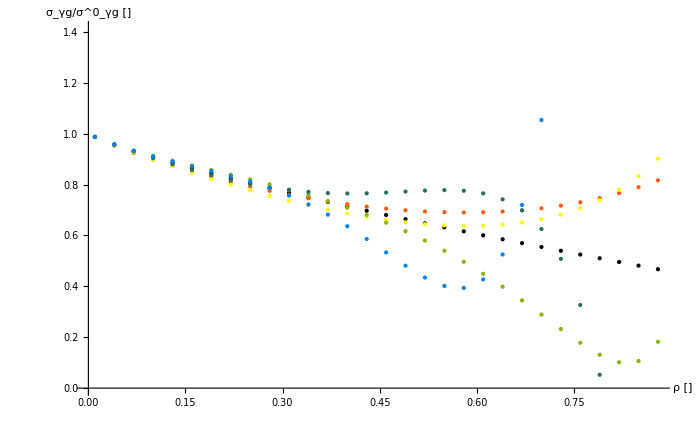

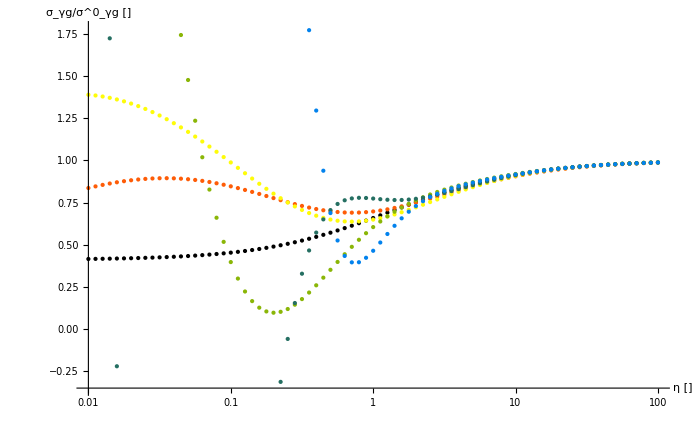

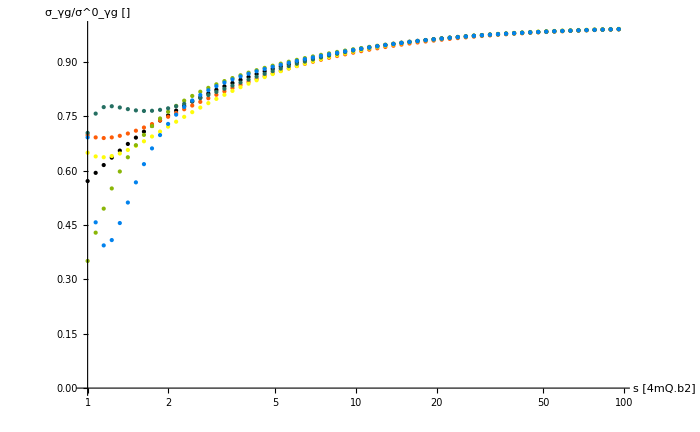

```mathematica
(*
 overall picture:
first element refers to full resummation
plot different variables: ρ,η,s
*)
Module[{v,orders,
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
computeOnGrid,
ρs,lρs,toρPlot,
ηs,lηs,toηPlot,
ss,lss,tosPlot
},
v=1; (* σ ~ β^v <-> Beta[n,v/2+1] *)
orders={2,3,5,7,10};(* At which orders should the expansion be taken? *)
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(*Print@fullN;Print@serN;*)
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
(* @param xs list to iterate *)
(* @param t transformation function applies to each element in list (to transform to ρ) *)
computeOnGrid[xs_List,t_Function] := Join[
{Parallelize@Table[fullρ[t@x],{x,xs}]},
(fρ↦Parallelize@Table[fρ[t@x],{x,xs}])/@serρs
];
(* equidistant ρ points; equivalent to alter mQ equidistant *)
ρs=Table[j,{j,.01,.9,.03}];
lρs=computeOnGrid[ρs,ρ↦ρ];
toρPlot[l_]:=Transpose[{ρs,l}];
(*Print@lρs;*)
Print@Show[ListPlot[(l↦toρPlot@Re@l)/@lρs,AxesLabel-> {"ρ []","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
(* logarithmic η points *)
ηs = Table[10^(j),{j,-2,2,.05}];
lρs=computeOnGrid[ηs,η↦η2ρ@η];
toηPlot[l_]:=Transpose[{ηs,l}];
(*Print@lFullηs;Print@lSerηs;*)
Print@Show[ListLogLinearPlot[(l↦toηPlot@Re@l)/@lρs,AxesLabel-> {"η []","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
(* equidistant s points *)
ss = Table[10^j,{j,0,2,.03}];
lss=computeOnGrid[ss,s↦s2ρ[(s*4mQ^2)]//.toN[]];
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@lFullss;Print@lSerss;*)
Print@Show[ListLogLinearPlot[(l↦tosPlot@Re@l)/@lss,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
]
```

### Case 1: Threshold limit

First let’s take a look at the threshold region: I conjecture really bad behaviour here, cause any power of ln(N) will introduce a power of ln(β) as I proved in [MSc]

#### Lemma: compare analytic expansion via d_(w,j)(v) to numeric inversion

First let’s check how good the deduced coefficients describe the threshold behavior, so I compare my coefficients d_(w,j)(v) to the numeric inversion of ln^w(N)
Q: Are the coefficients d_(w,j)(v) sufficient near threshold?

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
checkDToNumericInv[v_,orders_List]:=Module[{
ηs,numericFNs,lNumerics,fβs, lAnalytics,lErrs
},
ηs = Table[10^j,{j,-4,0,.03}];
(* compute numeric inversion *)
numericFNs = (o↦(n↦Beta[n,v/2+1]*Log[n+1]^o))/@orders;
lNumerics = (fN↦Parallelize@Table[getInvMellinTrafo[fN][η2ρ@η],{η,ηs}])/@numericFNs;
(* compute analytic inversion *)
fβs=(w↦(β↦β^v*(-1)^w*Sum[getD[w,j,v]*Log[β]^(w-j),{j,0,w}]))/@orders;
(* plot functions *)
(*Print@GraphicsRow[{
ListLogLinearPlot[(l↦Transpose[{ηs,l}])/@lNumerics,PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}],
LogLinearPlot[Evaluate[(f↦f[ρ2β@η2ρ@η])/@fβs],{η,Min@ηs,Max@ηs},PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}]
},ImageSize->800 ];*)
(* compute analytic at ηs *)
lAnalytics=(f↦Table[f[ρ2β@η2ρ@η],{η,ηs}])/@fβs;
(* compute relative error *)
lErrs = (Re@lNumerics-Re@lAnalytics)/Re@lNumerics;
(* plot errors *)
ListLogLogPlot[(l↦Transpose[{ηs,Abs@l}])/@lErrs,PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","rel. error []"}]
]
```

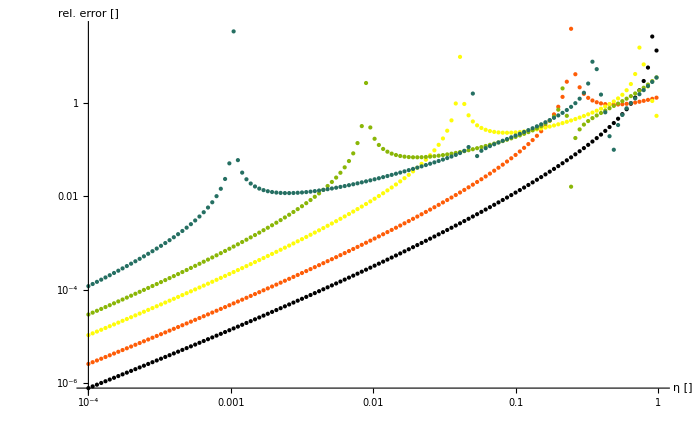

```mathematica
Show[checkDToNumericInv[1,{2,3,5,7,10}] ,ImageSize-> 700]
```

Answer (A): Yes, the coefficients are sufficient;
- the higher the power of ln^w(N), the later is the convergence, but nevertheless they converge
- the peaks to ∞ in the error-plot correspond to zeros of numeric inversion, that doesn’t get matched exactly by analytic inversion
- the peaks to 0 in the error-plot correspond to intersection between, analytic and numeric inversion

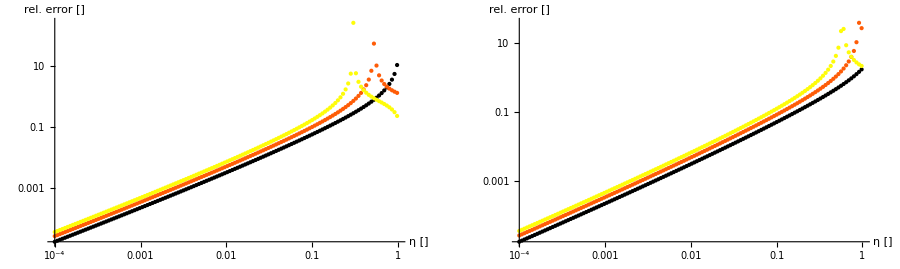

```mathematica
GraphicsRow[{
checkDToNumericInv[3,{2,3,4}],
checkDToNumericInv[5,{2,3,4}]
},ImageSize-> 900]
```

A: this is independent of v;
- propably: the higher v, the faster the convergence

#### Full resummation

The full resummation [is] seems constant > 0 near threshold

```mathematica
(* plot full resummation near threshold *)
(* @param v σ ~ β^v <-> Beta[n,v/2+1]  *)
Options[plotFullAtThreshLimit]={"toN"-> {}};
plotFullAtThreshLimit[v_,opts:OptionsPattern[]]:=Module[{f,ηs,l},
ηs = Table[10^j,{j,-7,0,.1}];
f=n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})//.toN[FilterRules[OptionValue["toN"], Options[toN]]]];
l = Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}];
ListLogLinearPlot[Transpose[{ηs,l}],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}]
];
```

This seems to be independet of v

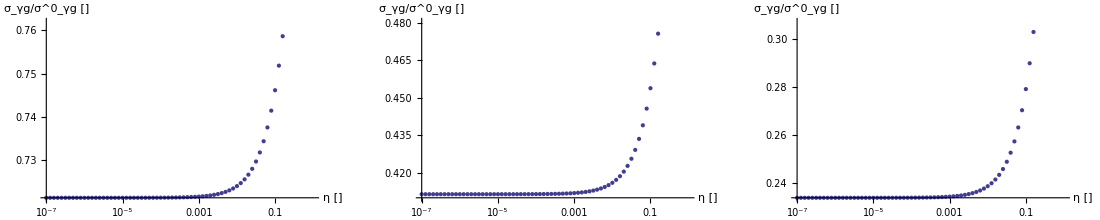

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[0],
plotFullAtThreshLimit[1],
plotFullAtThreshLimit[2]
},ImageSize-> 1100]
```

#### Problems with full resummation

BUT: I would have expected this threshold value to be independent of channel, as N→∞ beats everything, esp. exp(2x) or exp(4x) as the difference between γg and gg8 is;
it isn’t

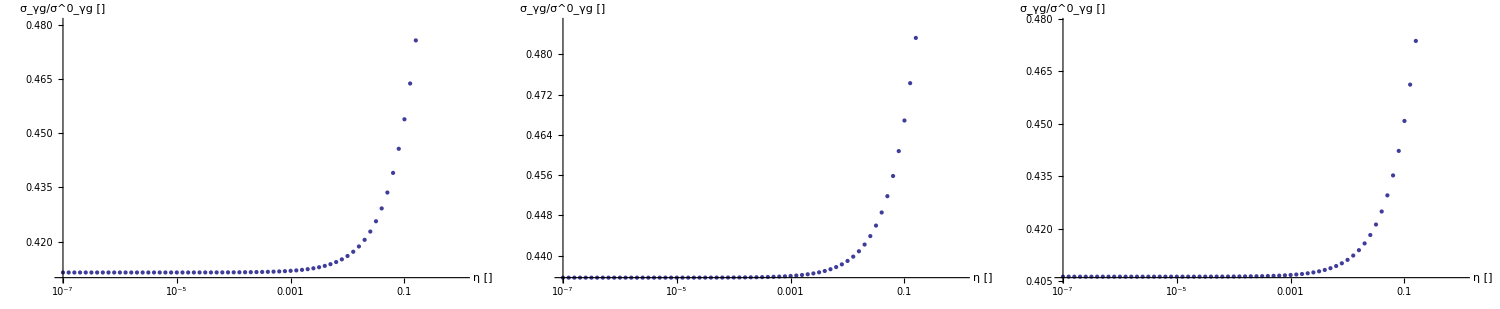

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "γg"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "gg8"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "qqbar8"}]
},ImageSize->1500,Spacings-> 0]
```

I also expected this threshold value to be independent of quark, as N→∞ beats everything, esp. exp(.36*x) or exp(.15*x) as the difference the quarks/the running coupling,
but it isn’t

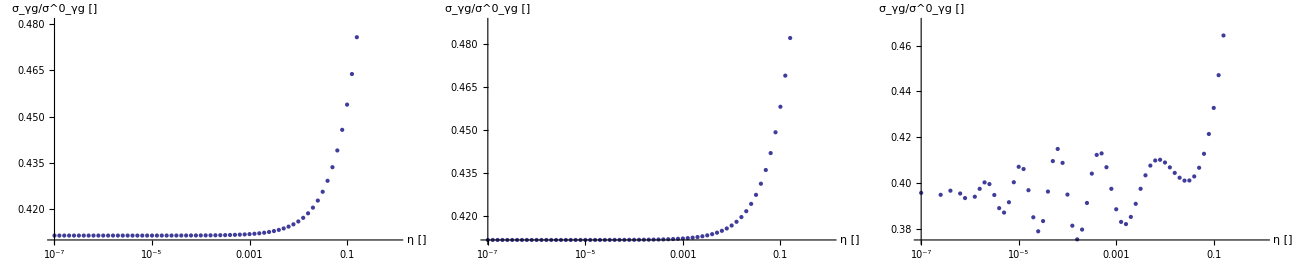

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "b"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t"}]
},ImageSize-> 1300,Spacings-> 0]
```

And, even worse, we seen some wild oscillations occuring before a constant is approached.
This problem rises from α beeing TOO SMALL (!) as can be seen in the following plot:
(NB: mQ→∞ ⇔ αμ→0)

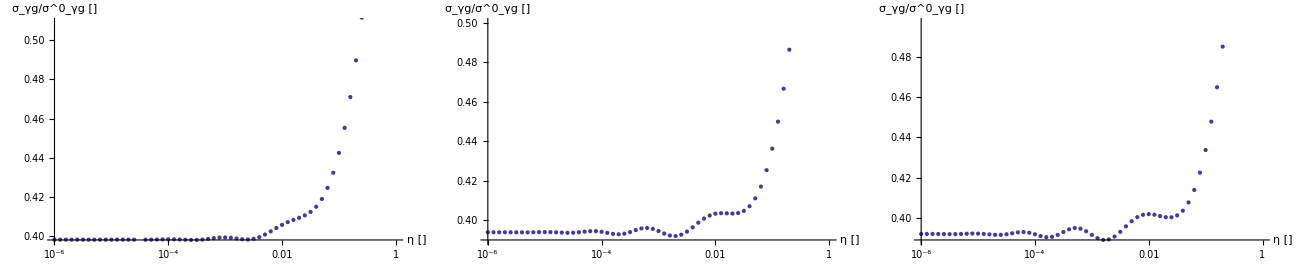

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 50}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 100}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 130}]
},ImageSize->1300,Spacings-> 0]
```

of course it also depends on b0, as b0 and α are appearing almost everywhere together: λ=α b0 ln(N) (b0 can be modified by the detected quark b0(charrn) > b0(top))

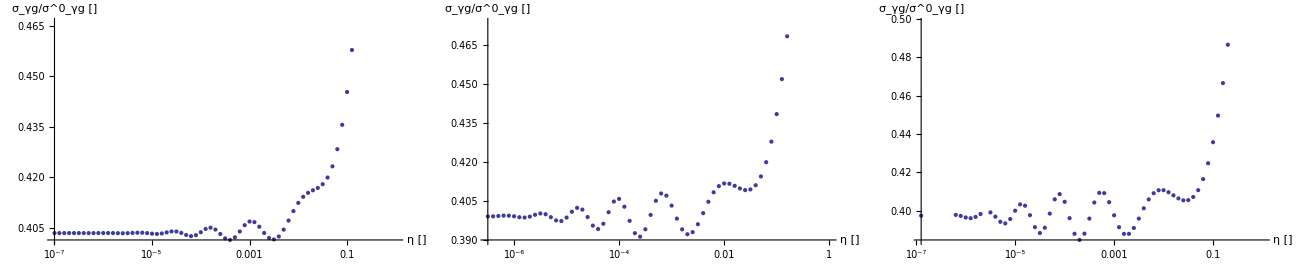

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 50}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 100}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 130}]
},ImageSize->1300,Spacings-> 0]
```

Alright lets track this oscillating-problem a bit: it depends strongly on v as can be seen here:

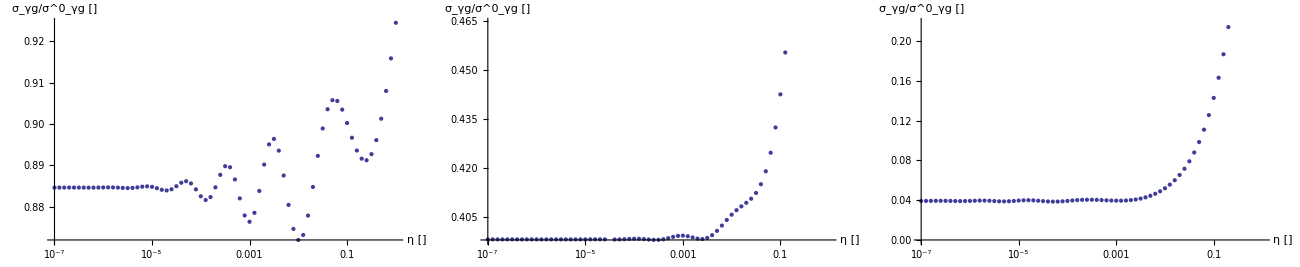

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[0,"toN"-> {"Q"-> "c","αμ"-> .15}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","αμ"-> .13}],
plotFullAtThreshLimit[2,"toN"-> {"Q"-> "c","αμ"-> .07}]
},ImageSize->1300,Spacings-> 0]
```

It depends on the channel

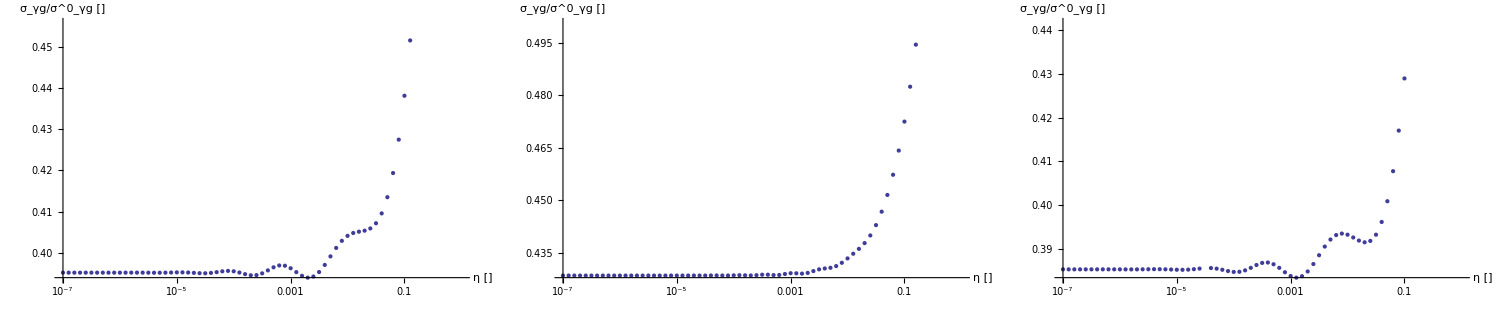

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "γg","αμ"-> .12}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "gg8","αμ"-> .12}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "qqbar8","αμ"-> .12}]
},ImageSize->1500,Spacings-> 0]
```

Wild guessing: what form has the exact inversion to take to make such oscillations?

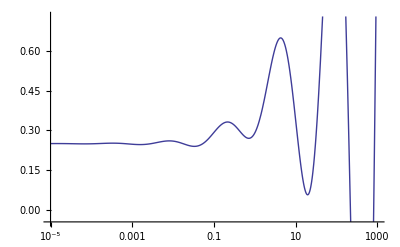

```mathematica
LogLinearPlot[.5-.25η2ρ[η]+.1Sin[2Log@η-1]*Exp[.5Log@η],{η,1*^-5,1*^3}]
```

Alrght:
- I don’t know, why these oscillations are occuring, and why they are appearing for small α
- this oscillation has already be found in [Bonc]
- nevertheless is seems BEYOND these oscillations (i.e. for even smaller η (smaller then in [Bonc])) the function still seems to approach a constant, but this region is numerically instable as well

Let’s see if we can find out a bit more about the threshold value (the constant value I’m suggesting)
Can we specify the dependencies a bit better?

```mathematica
(* plot full resummation for different running couplings αμ or equivalently mQ *)
(* Remember: α,μ ~ 1/ln(mQ) i.e. mQ->0⇒αμ->∞ and mQ->∞⇒αμ->0 *)
(* @param v σ ~ β^v <-> Beta[n,v/2+1]  *)
(* @param ρ ρ-point at which value is calculated  *)
getFullOnRunningPlots[v_,ρ_]:=Module[{f,ms,αμs,lms,lαμs},
f=n↦Beta[n,v/2+1]*(ΔLL//.{lnN -> Log[n+1]});
ms = Table[10^j,{j,0.2,2.5,.1}];
lms = Table[getInvMellinTrafo[n↦Evaluate[f[n]//.toN["mQ"-> m]]][1],{m,ms}];
αμs=Table[j,{j,.15,.8,.03}];
lαμs =Table[getInvMellinTrafo[n↦Evaluate[f[n]//.toN["αμ"-> cαμ]]][ρ],{cαμ,αμs}];
GraphicsRow[{
ListLogLinearPlot[Transpose[{ms,lms}],AxesLabel-> {"m [GeV]","σ_γg/σ^0_γg []"}],
ListPlot[Transpose[{αμs,lαμs}],AxesLabel-> {"αμ []","σ_γg/σ^0_γg []"}]
}]
]
```

We always use real threshold i.e. ρ=1 and we get the following picture:

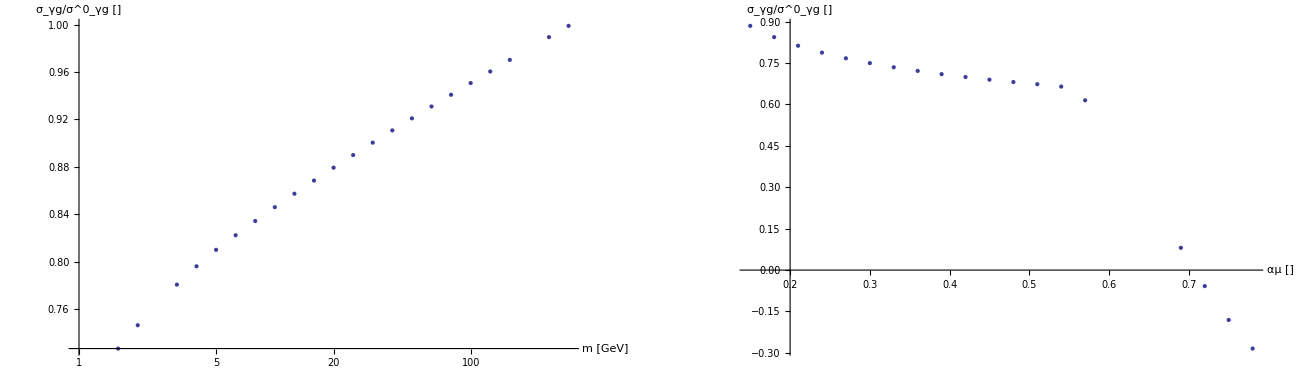

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2158.06  + 1351.24\ ⅈ
 and 1202.38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17423.7  + 2537.64\ ⅈ
 and 8183.07 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 76617.3  + 86151.2\ ⅈ
 and 52336.4 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

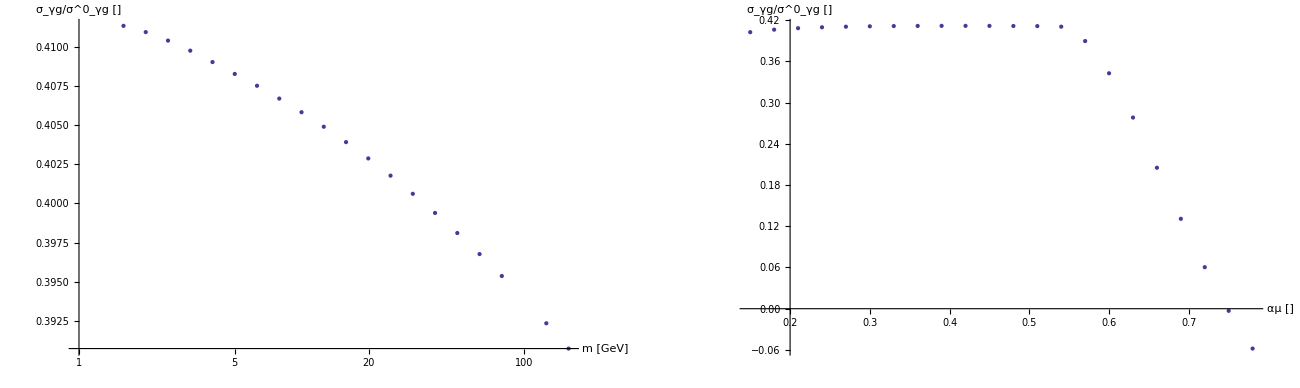

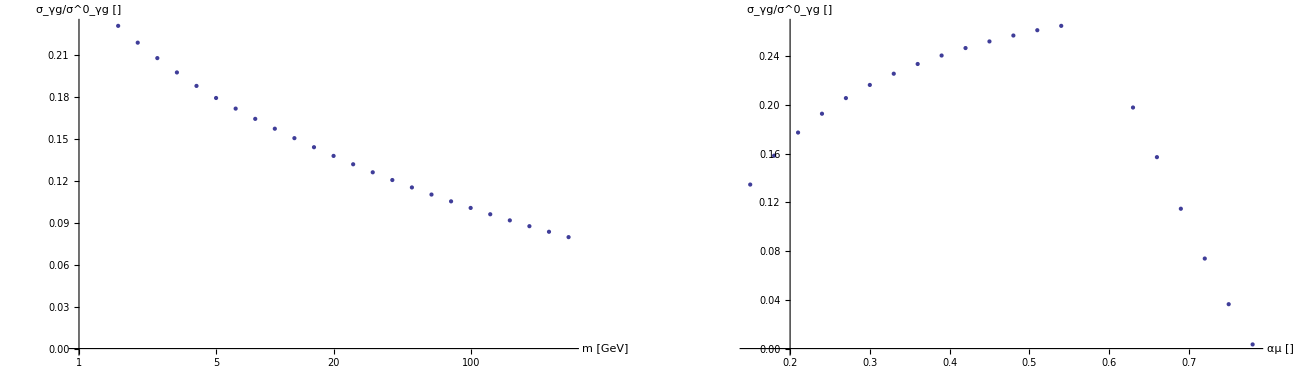

```mathematica
Show[getFullOnRunningPlots[0,1],ImageSize-> 1300]
Show[getFullOnRunningPlots[1,1],ImageSize-> 1300]
Show[getFullOnRunningPlots[2,1],ImageSize-> 1300]
```

And this is even more supprising:
- the shapes for v=1 and v=2 are kind of similar, but v=0 (would correspond to leading Coulomb term) has a different shape
- furthermore we find σ(σ=1) < 0 for αμ getting to large. We would expect problems for αμ getting to large, but does this hold at threshold? I would have expected problems comming to threshold as αμ increases, but at threshold?

#### Reexpansion

The analytic inversion in contrast is f(β→0)→0 as β^v is always stronger then ln(β)^w

```mathematica
Limit[β^v*Log[β],β-> 0,Assumptions-> {v>0}]
```

0

Furthermore the coefficients are wildy oscillating near threshold

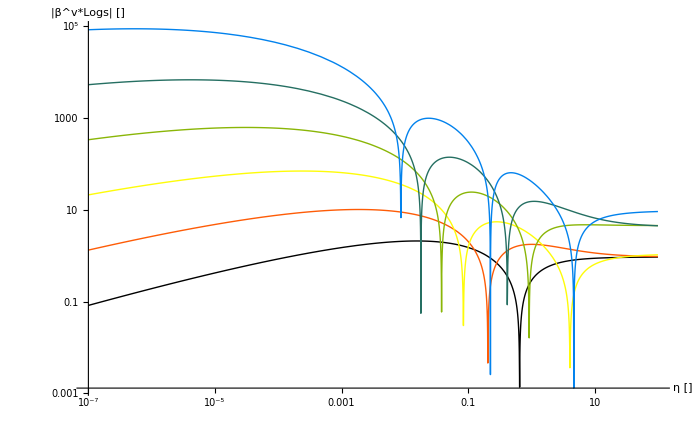

```mathematica
Module[{v,orders,fβs},
v = 1;(* σ ~ β^v <-> Beta[n,v/2+1] *)
orders={2,3,4,5,6,7};
(* compute analytic inversion *)
fβs=(w↦(β↦β^v*(-1)^w*Sum[getD[w,j,v]*Log[β]^(w-j),{j,0,w}]))/@orders;
Show[LogLogPlot[Evaluate[(f↦Abs@f[ρ2β@η2ρ@η])/@fβs],{η,1*^-7,1*^2},PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","|β^v*Logs| []"}],ImageSize-> 700]
]
```

Problems with the coefficients:
- the higher w, the more real zeros on η in [0,1] exist
- the higher w, the smaller the smallest zero gets
- the higher w, the later is the convergence f(η→0)→0
- the higher w, the higher is e.g. f(η=1e-5)

A: the reexpansion will NOT be related to the full resummation in the threshold limit

#### [probably wrong] don’t use Beta-function in resummation?

- What would be if we just compute the inverse of the raw Sudakov-exponent?
- well, probably this will NOT work, as we need some regularising function - either Beta-function or N^(-k)
- cause “If ϕ(s) is analytic in the strip a < Re(s) < b, and if it tends to zero uniformly as Im(s)→±∞ for any real value c between a and b, with its integral along such a line converging absolutely, then [the inversion exists]”[InvMelTh] and this is clearly not the case as |ln(N)| >= ln(|N|); i.e. the expression grows in all directions
- nevertheless can Mathematica compute the inverse, but this is probably due to the contour-deforming-trick of [MP]; this trick is (I think) numerically needed, but we’re not allowed to be mathematical dependent on it

{1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π,1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π+(2 b0 lnN^3 αμ^2 ν SudakovFactor`Private`Ak[1])/(3 π),1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π+(2 b0 lnN^3 αμ^2 ν SudakovFactor`Private`Ak[1])/(3 π)+(lnN^4 (4 b0^2 π αμ^3 ν SudakovFactor`Private`Ak[1]+3 αμ^2 ν^2 (SudakovFactor`Private`Ak[1])^2))/(6 π^2)}

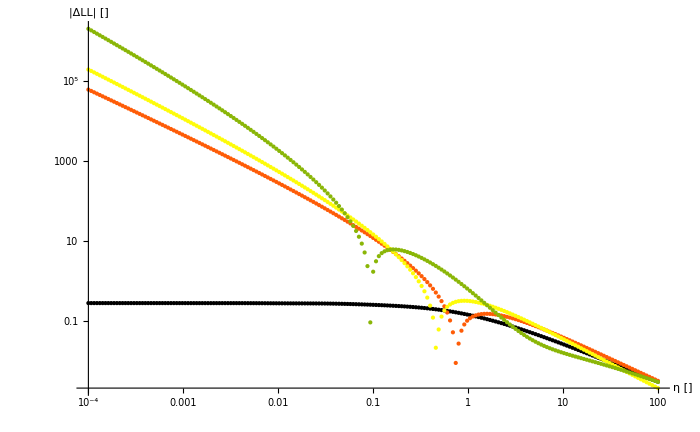

```mathematica
Module[{orders,f,gMaxOrder,gs,gNs,ηs,lf,lNumericgN,analyticgNs,lnN2ρ,ind2w},
orders={2,3,4};
(* build functions *)
f =n↦Evaluate[(ΔLL//.{lnN -> Log[n+1]})//.toN[]];
gMaxOrder=Normal@Series[ΔLL,{lnN,0,Max@orders}];
gs = Table[Normal@Series[gMaxOrder,{lnN,0,w}],{w,orders}];
Print@gs;
gNs=(g↦(n↦Evaluate[g//.{lnN-> Log[n+1]}//.toN[]]))/@gs;
(* plot *)
(*Print[{zPlotReIm[f]}~Join~Table[zPlotReIm@gN,{gN,gNs}]];*)
(* compute on grid *)
ηs=Table[10^j,{j,-4,2,.03}];
lf=Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}];
lNumericgN  = (gN↦Parallelize@Table[getInvMellinTrafo[gN][η2ρ@η],{η,ηs}])/@gNs;
(*lnN2ρ[w_]=Limit[D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,w}],k-> 0];
ind2w[ind_]:=First@ind-1;
analyticgNs=(g↦MapIndexed[Function[{c,ind},c*lnN2ρ[ind2w@ind]],CoefficientList[g,{lnN}]])/@gs;
Print@analyticgNs;*)
(*Print@ListLogLinearPlot[Transpose[{ηs,l}]];*)
Print@Show[ListLogLogPlot[Evaluate[Abs@({Transpose[{ηs,lf}]}~Join~((l↦Transpose[{ηs,l}])/@lNumericgN))],PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","|ΔLL| []"}],ImageSize-> 700];
(*LogLogPlot[Evaluate[(g↦Abs[g/.{ρ-> η2ρ@η}//.toN[]])/@analyticgNs],{η,1*^-4,1*^2}]*)
]
```

I don’t know how such functions can be inverted ...

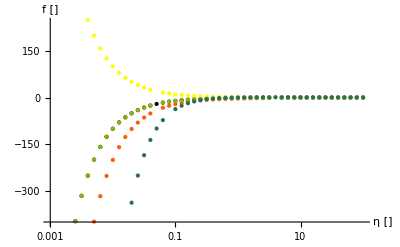

```mathematica
Module[{fNs,ηs,ls},
fNs={n↦1+Log[n],n↦2*Log@n,n↦1-Log[n],n↦Log[n],n↦1+Log[n]^2};
ηs=Table[10^j,{j,-3,2,.1}];
ls=(f↦Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}])/@fNs;
Print@ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,l}])/@ls],PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","f []"}];
]
```

[MP] gave the inversion of ln^w(N)/N^k but this is only valid for Re(k) >0
and yes if we plug k=0 into their formula, we don’t get the same as above

(Log[1/ρ]^(-1+k) Log[Log[1/ρ]]^2)/Gamma[ρ]

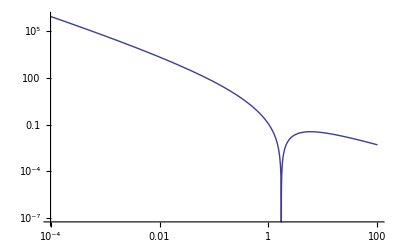

```mathematica
D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,2}]
LogLogPlot[Abs[Limit[D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,2}],k-> 0]]/.{ρ-> η2ρ@η},{η,1*^-4,1*^2}]
```

as already said is ln^w(N) growing in all directions

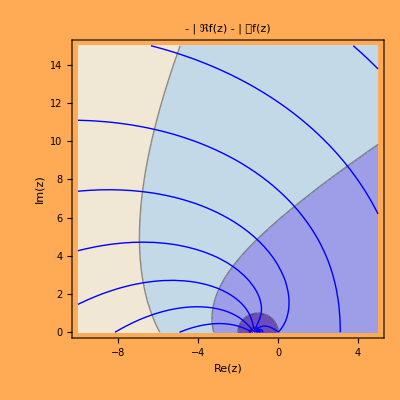

```mathematica
zPlotReIm[n↦Log[n+1]^2,"ymin"-> 0,"xmin"-> -10,"ymax"-> 15]
```

### Case 2: High-energy limit

NB: this section is really theoretical, as I can NOT say, whether resummation is physically valid at all in this limit; so for the moment let’s forget the physics and compare the functions in a mathematical point of view
NB: this limit is numerically unstable[MSc], so I have to guess a bit, and this is why MMa is complainig about “suspect highly oscillatory integrand”; yes, it is
NB: unfortunaly I first forgot the shift to N+1, and it turns out this changed the picture completly - so yes the shift is important (and from this, I think, we can conclude HE-Limit ⇔ ρ→0⇔N→1(0?))

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
getDiffHELimit[v_,orders_]:=Module[{
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
ss,lFull,lSer,tosPlot
},
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
ss = Table[10^j,{j,1,3,.03}];
lFull = Parallelize@Table[fullρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}];
lSer = (fρ↦Parallelize@Table[fρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}])/@serρs;
(* Plot *)
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@Show[ListPlot[tosPlot@Re@lFull,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"}],ImageSize-> 700];*)
ListLogLogPlot[(l↦tosPlot@Abs[(Re@l-Re@lFull)/Re@lFull])/@lSer,AxesLabel-> {"s [4mQ.b2]","rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
]
```

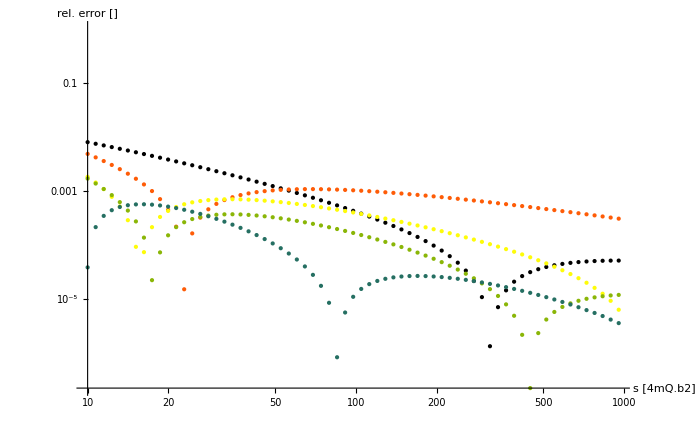

```mathematica
Show[getDiffHELimit[1,{2,3,5,7,10}],ImageSize-> 700]
```

A: Yes, the reexpansion will converge towards the full resummation
- it oscillates around full resummation
- the higher the expansion, the smaller gets the amplitude
- the higher the expansion, the faster gets the frequency

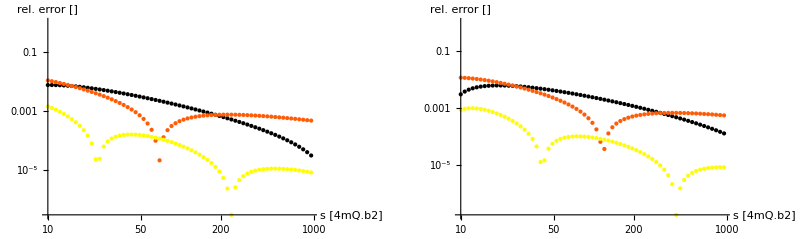

```mathematica
GraphicsRow[{
getDiffHELimit[3,{2,3,10}],
getDiffHELimit[5,{2,3,10}]
},ImageSize-> 800]
```

A: this is independent of v
A: as proved above, the series coefficients of Born cross section sum up to 0, so for full Born resummation the function DOES NOT converge to 1 but to 0 as they are cancelling eachother

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders How many orders should be considered for expansion? *)
getDiffStrictHELimit[v_,ks_]:=Module[{
fullN,cutLnΔLL,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
ss,lFull,lSer,tosPlot
},
orders=2*ks;
(* get series *)
cutLnΔLL = Normal@Series[Log[ΔLL],{lnN,0,2}];
serΔLLMax = Normal@Series[Exp@cutLnΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
ss = Table[10^j,{j,1,3,.03}];
lFull = Parallelize@Table[fullρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}];
lSer = (fρ↦Parallelize@Table[fρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}])/@serρs;
(* Plot *)
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@Show[ListPlot[tosPlot@Re@lFull,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"}],ImageSize-> 700];*)
ListLogLogPlot[(l↦tosPlot@Abs[(Re@l-Re@lFull)/Re@lFull])/@lSer,AxesLabel-> {"s [4mQ.b2]","rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
]
```

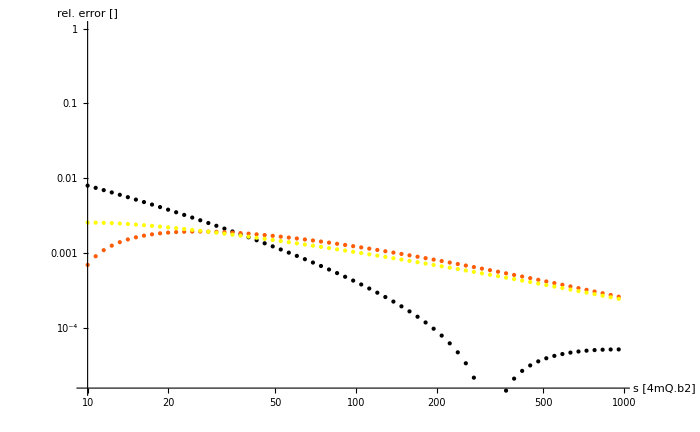

```mathematica
Show[getDiffStrictHELimit[1,{1,2,3}],ImageSize-> 700]
```

A: if one takes, the physically better expansion (NB: I still don’t know, whether this makes sense), i.e. to cut ln(Δ) to ln(N)^2 (as the coefficients below are NOT determined correct) the convergence gets worse, as the full resummation contains these unsatisfied elements

So the overall answer is:
- in the region where we trust resummation, i.e. threshold region, it DOES NOT converge
- and in the region where we don’t trust resummation, i.e. HE region, it DOES converge

### Case 3: Can we give a point that splits threshold- and HE-limit

#### Can we mimic the full resummation?

{1.89707,1.75851,1.72022,1.71806,1.72776,1.74094,1.75454,1.76745,1.77931,1.79005,1.79974,1.80846,1.81633,1.82343,1.82988,1.83574,1.84109,1.84598,1.85048,1.85462,1.85844,1.86198,1.86527,1.86833,1.87118,1.87385,1.87635,1.87869,1.8809,1.88298,1.88494,1.8868,1.88855,1.89021,1.89179,1.89329,1.89472,1.89608,1.89738,1.89862}

{3.56946,3.46185,3.49457,3.54251,3.58523,3.62063,3.64969,3.67371,3.69378,3.71074,3.72523,3.73774,3.74864,3.75822,3.76669,3.77424,3.78101,3.78711,3.79264,3.79767}

{3.72013,3.48014,3.47308,3.51874,3.56479,3.6038,3.63587,3.66226,3.68418,3.7026,3.71826,3.73171,3.74337,3.75358,3.76258,3.77058,3.77772,3.78414,3.78994,3.79521}

{freqP$229752[1]→0.522126,freqP$229752[2]→0.364954,freqP$229752[3]→2.61004,freqP$229752[4]→3.60698,freqP$229752[5]→-0.000920612,freqP$229752[6]→1.03476,freqP$229752[7]→-0.0719405,freqP$229752[8]→0.3173}

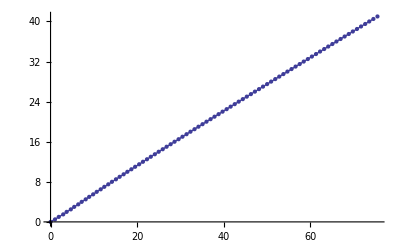

{{0,0,0},{1.0331,1/2,0.53904},{1.90074,1,0.968875},{2.93017,3/2,1.51825},{3.72013,2,1.96367},{4.68868,5/2,2.52337},{5.47021,3,2.97869},{6.40891,7/2,3.5257},{7.20027,4,3.98586},{8.12697,9/2,4.52325},{8.93205,5,4.98866},{9.85473,11/2,5.5199},{10.6734,6,5.98891},{11.5957,13/2,6.51465},{12.4266,7,6.98631},{13.3502,15/2,7.5091},{14.1921,8,7.98487},{15.1177,17/2,8.50707},{15.9691,9,8.98624},{16.897,19/2,9.50646},{17.7569,10,9.98671},{18.687,21/2,10.5046},{19.5544,11,10.9867},{20.4868,23/2,11.5046},{21.3607,12,11.9894},{22.2952,25/2,12.5066},{23.175,13,12.992},{24.1115,27/2,13.5068},{24.9966,14,13.9923},{25.935,29/2,14.5066},{26.8247,15,14.994},{27.7649,31/2,15.5086},{28.6588,16,15.9967},{29.6006,33/2,16.5094},{30.4984,17,16.9967},{31.4417,35/2,17.5082},{32.343,18,17.9968},{33.2877,37/2,18.5089},{34.1922,19,18.9987},{35.1381,39/2,19.5096},{36.0456,20,19.9984},{36.9928,41/2,20.5077},{37.9029,21,20.997},{38.8512,43/2,21.507},{39.7639,22,21.9979},{40.7132,45/2,22.5077},{41.6282,23,22.9978},{42.5784,47/2,23.5058},{43.4956,24,23.9957},{44.4468,49/2,24.5041},{45.3659,25,24.9956},{46.3179,51/2,25.5046},{47.2389,26,25.996},{48.1918,53/2,26.5033},{49.1145,27,26.994},{50.0681,55/2,27.5012},{50.9925,28,27.9934},{51.9468,57/2,28.5017},{52.8728,29,28.9944},{53.8277,59/2,29.5015},{54.7551,30,29.9931},{55.7107,61/2,30.4995},{56.6395,31,30.9922},{57.5957,63/2,31.5},{58.5257,32,31.9938},{59.4825,65/2,32.5009},{60.4137,33,32.9936},{61.371,67/2,33.4997},{62.3034,34,33.9929},{63.2612,69/2,34.5002},{64.1947,35,34.9949},{65.153,71/2,35.5023},{66.0875,36,35.9961},{67.0463,73/2,36.5021},{67.9818,37,36.9959},{68.941,75/2,37.5028},{69.8775,38,37.9983},{70.8371,77/2,38.5058},{71.7745,39,39.0008},{72.7345,79/2,39.5069},{73.6727,40,40.0013},{74.6331,81/2,40.5079},{75.5721,41,41.004}}

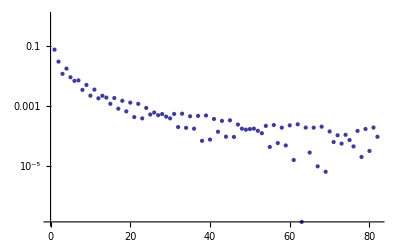

{{0,9.64807},{1.90074,6.77948},{3.72013,3.78775},{5.47021,2.27363},{7.20027,1.48912},{8.93205,1.04329},{10.6734,0.768612},{12.4266,0.588258},{14.1921,0.463775},{15.9691,0.374378},{17.7569,0.308083},{19.5544,0.257603},{21.3607,0.218308},{23.175,0.187141},{24.9966,0.162021},{26.8247,0.141491},{28.6588,0.124508},{30.4984,0.110306},{32.343,0.0983166},{34.1922,0.0881081},{36.0456,0.079349},{37.9029,0.0717808},{39.7639,0.0652003},{41.6282,0.0594452},{43.4956,0.0543854},{45.3659,0.0499151},{47.2389,0.0459477},{49.1145,0.0424119},{50.9925,0.0392485},{52.8728,0.036408},{54.7551,0.0338488},{56.6395,0.0315358},{58.5257,0.029439},{60.4137,0.0275329},{62.3034,0.0257956},{64.1947,0.0242082},{66.0875,0.0227544},{67.9818,0.0214199},{69.8775,0.0201924},{71.7745,0.0190611},{73.6727,0.0180163},{75.5721,0.0170498}}

{envP$229752[1]→106.032,envP$229752[2]→10.99,envP$229752[3]→-100.152,envP$229752[4]→1062.83,envP$229752[5]→-188.869,envP$229752[6]→1131.28}

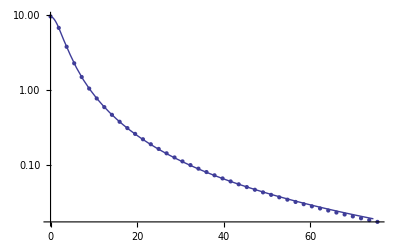

{{0,9.64807,9.64806},{1.90074,6.77948,6.7795},{3.72013,3.78775,3.78761},{5.47021,2.27363,2.27486},{7.20027,1.48912,1.48554},{8.93205,1.04329,1.04437},{10.6734,0.768612,0.771366},{12.4266,0.588258,0.590417},{14.1921,0.463775,0.464725},{15.9691,0.374378,0.374231},{17.7569,0.308083,0.307149},{19.5544,0.257603,0.256187},{21.3607,0.218308,0.216652},{23.175,0.187141,0.185418},{24.9966,0.162021,0.16035},{26.8247,0.141491,0.139947},{28.6588,0.124508,0.123135},{30.4984,0.110306,0.109129},{32.343,0.0983166,0.0973455},{34.1922,0.0881081,0.0873426},{36.0456,0.079349,0.078783},{37.9029,0.0717808,0.0714047},{39.7639,0.0652003,0.0650022},{41.6282,0.0594452,0.0594123},{43.4956,0.0543854,0.0545045},{45.3659,0.0499151,0.050173},{47.2389,0.0459477,0.0463319},{49.1145,0.0424119,0.0429105},{50.9925,0.0392485,0.0398503},{52.8728,0.036408,0.0371025},{54.7551,0.0338488,0.0346265},{56.6395,0.0315358,0.0323877},{58.5257,0.029439,0.030357},{60.4137,0.0275329,0.0285096},{62.3034,0.0257956,0.0268243},{64.1947,0.0242082,0.0252827},{66.0875,0.0227544,0.023869},{67.9818,0.0214199,0.0225697},{69.8775,0.0201924,0.0213727},{71.7745,0.0190611,0.0202676},{73.6727,0.0180163,0.0192454},{75.5721,0.0170498,0.018298}}

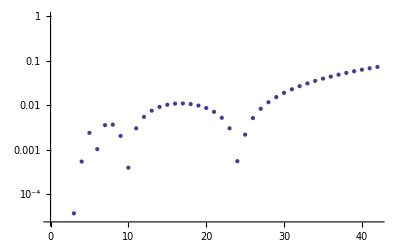

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {320.688}. NIntegrate obtained 0.744713 and 0.0405847 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {127.}. NIntegrate obtained -0.108532 and 0.0000403717 for the integral and error estimates.

{0.83858+1.33227×10^-15 ⅈ,0.744713,-0.108532}

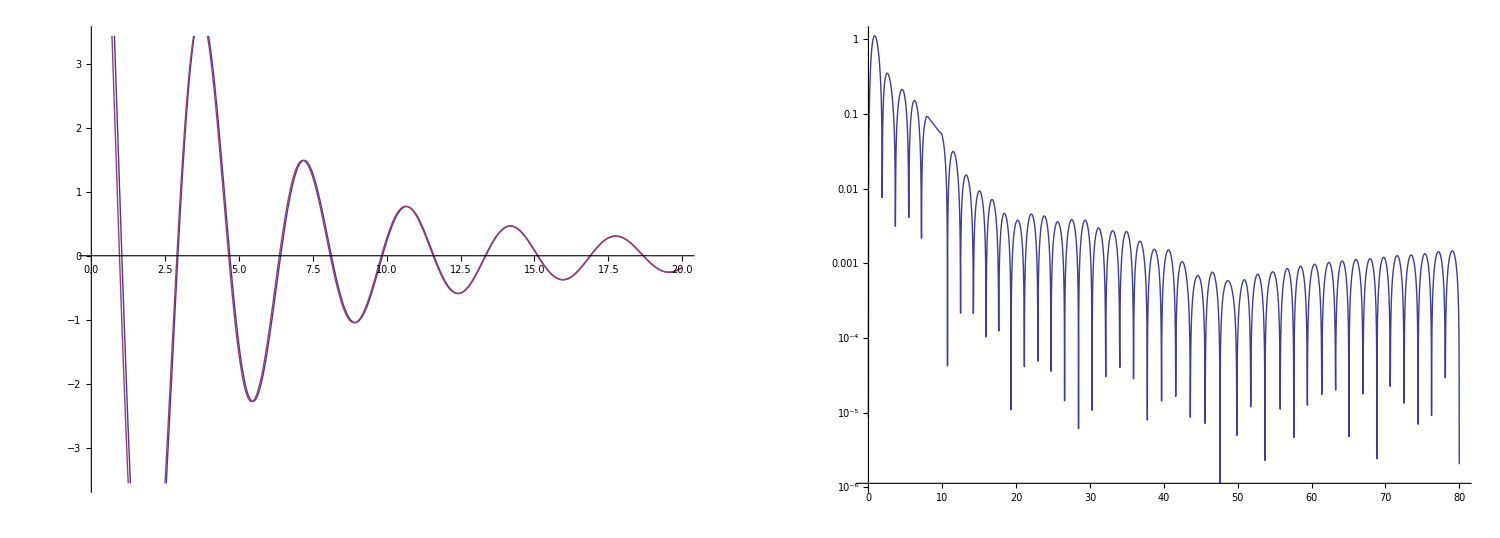

```mathematica
Options[getFitFull]={"toN"-> {}};
getFitFull[v_,opts:OptionsPattern[]]:=Module[{
fullN,
Cmp,ϵ,path,fullY,
ρ,mins,maxs,zeros,
freqData,freqFit,freqP,freqSol,
envData,envFit,envP,envSol,
fit,p
},
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
Cmp=2.7;
ϵ=0;
path[x_]=Cmp+(I-ϵ)x;
fullY ={y,ρ}↦Re[(ρ^(-n)fullN[n])/.{n-> path[y]}]/π;
(* find prominent points *)
ρ=.2;
mins={
NArgMin[{fullY[y,ρ]//.toN[OptionValue["toN"]],y>0&&y<2},y],
NArgMin[{fullY[y,ρ]//.toN[OptionValue["toN"]],y>4&&y<6},y],
NArgMin[{fullY[y,ρ]//.toN[OptionValue["toN"]],y>8&&y<10},y]
};
maxs={
0,
NArgMax[{fullY[y,ρ]//.toN[OptionValue["toN"]],y>mins[[1]]&&y<mins[[2]]},y],
NArgMax[{fullY[y,ρ]//.toN[OptionValue["toN"]],y>mins[[2]]&&y<mins[[3]]},y]
};
Do[Module[{l,d},
l=Length@mins;
d=maxs[[l]]-maxs[[l-1]];
AppendTo[maxs,NArgMax[{fullY[y,ρ]//.toN[OptionValue["toN"]],y>mins[[l]]&&y<mins[[l]]+d},y]];
l=Length@maxs;
d=mins[[l-1]]-mins[[l-2]];
AppendTo[mins,NArgMin[{fullY[y,ρ]//.toN[OptionValue["toN"]],y>maxs[[l]]&&y<maxs[[l]]+d},y]];
]
,{18}];
(* find frequency *)
zeros=Table[y/.FindRoot[fullY[y,ρ]//.toN[OptionValue["toN"]],{y,(maxs[[j]]+mins[[j]])/2}],{j,Length@mins}]~Join~Table[y/.FindRoot[fullY[y,ρ]//.toN[OptionValue["toN"]],{y,(mins[[j]]+maxs[[j+1]])/2}],{j,Length@maxs-1}];
zeros =Sort@zeros;
Print@Table[zeros[[j+1]]-zeros[[j]],{j,Length@zeros-1}];
Print@Table[mins[[j+1]]-mins[[j]],{j,Length@mins-1}];
Print@Table[maxs[[j+1]]-maxs[[j]],{j,Length@maxs-1}];
(*Print[zeros," <-> ",mins," <-> ", maxs];*)
(*Print@Transpose[{maxs,zeros,mins}];*)
freqData=Sort@Join[
Transpose[{zeros,-1/2+Range[Length@zeros]}],
Transpose[{maxs,2*(Range[Length@maxs]-1)}],
Transpose[{mins,1+2*(Range[Length@mins]-1)}]
];
freqFit=y↦freqP[1]*y+freqP[2]*Log[1+y]-(freqP[3]*y)/(freqP[4]^2+ y^2)+freqP[5]*Sin[freqP[6]*y]+freqP[7]*y*Exp[-freqP[8]^2 y];
freqSol = FindFit[freqData,{freqFit[y]},Table[{freqP[j],1},{j,8}],y];
Print@freqSol;
Print@Show[{ListPlot[freqData],Plot[{freqFit[y]/.freqSol,freqP[1]*y},{y,0,Max@zeros}]}];
Print[(d↦Join[d,{freqFit[d[[1]]]/.freqSol}])/@freqData];
Print@ListLogPlot[(d↦Abs[(d[[2]]-(freqFit[d[[1]]]/.freqSol))/d[[2]]])/@Drop[freqData,1]];

(* find evelope *)
envData=Table[{y,Abs@fullY[y,ρ]//.toN[OptionValue["toN"]]},{y,Sort@Join[maxs,mins]}];
Print@envData;
envFit=y↦envP[1]/(envP[2]+y^2)+(envP[3]*y)/(envP[4]+y^4)+(envP[5]*y)/(envP[6]+y^6);
envSol = FindFit[envData,envFit[y],Table[envP[j],{j,6}],y];
Print@envSol;
Print@Show[{ListLogPlot[envData],LogPlot[envFit[y]/.envSol,{y,0,Max@zeros}]}];
Print[(d↦Join[d,{envFit[d[[1]]]/.envSol}])/@envData];
Print@ListLogPlot[(d↦Abs[(d[[2]]-(envFit[d[[1]]]/.envSol))/d[[2]]])/@envData];

fit=y↦(envFit[y]/.envSol)*Cos[π*freqFit[y]/.freqSol];

Print@{
getInvMellinTrafo[fullN//.toN[OptionValue["toN"]]][ρ],
NIntegrate[fullY[y,ρ]//.toN[OptionValue["toN"]],{y,0,∞}],
NIntegrate[fit[y],{y,0,∞}]
};

GraphicsRow[{
Plot[{fullY[y,ρ]//.toN[OptionValue["toN"]],fit[y]},{y,0,20}],
LogPlot[Abs@((fullY[y,ρ]//.toN[OptionValue["toN"]])-fit[y]),{y,0,80}],
}]
]
Show[getFitFull[1],ImageSize-> 1500]
```

- fit looks kind of alright, but still are the integrals quite different and Mathematica is again complaining about oscillations? But how can he then solve the integral with full Res?
- NB: Mathematica fits oscillations faster the just linear, but this shouldn’t be the case, should it? the zeros seems to repeal each other ...

#### N-space convergence

6.94572 -> eff.: 4.24572

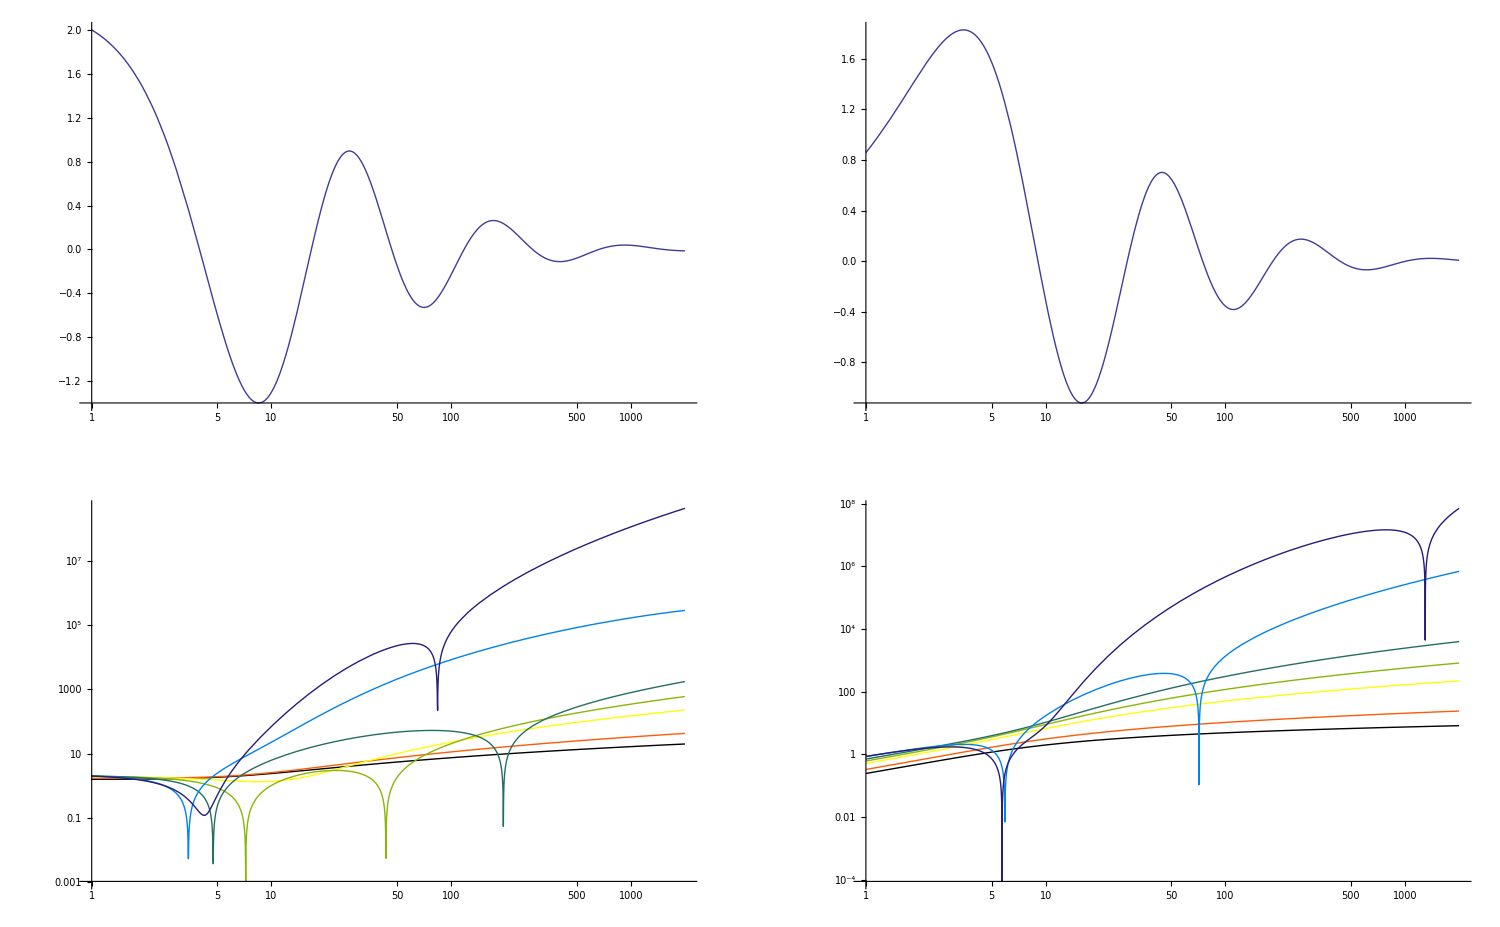

```mathematica
Options[plotKernels]={"toN"-> {}};
plotKernels[v_,orders_,opts:OptionsPattern[]]:=Module[{
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
Cmp,ϵ,path
},
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[(*Beta[n,v/2+1]*)(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[(*Beta[n,v/2+1]*)(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
(*fullρ = getInvMellinTrafo[fullN//.toN[OptionValue["toN"]]];
serρs=(f↦getInvMellinTrafo[f//.toN[OptionValue["toN"]]])/@serNs;*)
Cmp=2.7;
ϵ=0;
path[x_]=Cmp+(I-ϵ)x;
Print[nLandau//.toN[OptionValue["toN"]]," -> eff.: ",(nLandau//.toN[OptionValue["toN"]])-Cmp];
GraphicsGrid[{
{
LogLinearPlot[Re[((*ρ^(-n)*)fullN[n])//.toN[OptionValue["toN"]]/.{n-> path[y],ρ-> 0.2}],{y,1,2000}],
LogLinearPlot[Im[((*ρ^(-n)*)fullN[n])//.toN[OptionValue["toN"]]/.{n-> path[y],ρ-> 0.2}],{y,1,2000}]
},
{
LogLogPlot[Evaluate@Abs@Re[((*ρ^(-n)*)(#[n]&)/@serNs)//.toN[OptionValue["toN"]]/.{n-> path[y],ρ-> 0.2}],{y,1,2000},PlotStyle->ColorData[3,"ColorList"]],
LogLogPlot[Evaluate@Abs@Im[((*ρ^(-n)*)(#[n]&)/@serNs)//.toN[OptionValue["toN"]]/.{n-> path[y],ρ-> 0.2}],{y,1,2000},PlotStyle->ColorData[3,"ColorList"]]
}
}]
]
Show[plotKernels[1,{2,3,4,5,6,10,15}],ImageSize-> 1500]
```

- nothing new here, but [MSc] holds: for N < NL everything is alright and above there chaos
- full resummation is slowly oscillating (with exponentional period), that why we found above oscillation faster then linear (Mellin-Kernel=linear + Full)
- full resummation is decreasing, logarithmically slow, but nevertheless decreasing: see also below
- cut resummation is exponentially increasing

```mathematica
ComplexExpand[b0*π/ν/SudakovFactor`Private`Ak[1]*(lnN*commonG[1][lnN/2/lnNL])//.{lnN-> Log[cMP+I R]}]
```

Arg[cMP+ⅈ R] Arg[1-Log[cMP+ⅈ R]/lnNL]+1/2 Log[cMP^2+R^2]+lnNL Log[√(Arg[cMP+ⅈ R]^2/lnNL^2+(1-Log[cMP^2+R^2]/(2 lnNL))^2)]-1/2 Log[cMP^2+R^2] Log[√(Arg[cMP+ⅈ R]^2/lnNL^2+(1-Log[cMP^2+R^2]/(2 lnNL))^2)]+ⅈ (Arg[cMP+ⅈ R]+lnNL Arg[1-Log[cMP+ⅈ R]/lnNL]-1/2 Arg[1-Log[cMP+ⅈ R]/lnNL] Log[cMP^2+R^2]-Arg[cMP+ⅈ R] Log[√(Arg[cMP+ⅈ R]^2/lnNL^2+(1-Log[cMP^2+R^2]/(2 lnNL))^2)])

```mathematica
(* Re of above and lim_{R->∞} = -∞, i.e. Exp[...] is converging! *)
Simplify[Arg[cMP+ⅈ R] Arg[1-Log[cMP+ⅈ R]/lnNL]+1/2 Log[cMP^2+R^2]+lnNL Log[√(Arg[cMP+ⅈ R]^2/lnNL^2+(1-Log[cMP^2+R^2]/(2 lnNL))^2)]-1/2 Log[cMP^2+R^2] Log[√(Arg[cMP+ⅈ R]^2/lnNL^2+(1-Log[cMP^2+R^2]/(2 lnNL))^2)]]
```

1/4 (4 Arg[cMP+ⅈ R] Arg[1-Log[cMP+ⅈ R]/lnNL]-Log[cMP^2+R^2] (-2+Log[(4 Arg[cMP+ⅈ R]^2+(-2 lnNL+Log[cMP^2+R^2])^2)/(4 lnNL^2)])+2 lnNL Log[(4 Arg[cMP+ⅈ R]^2+(-2 lnNL+Log[cMP^2+R^2])^2)/(4 lnNL^2)])

```mathematica
Module[{cMP,ϵ,path},
cMP=2.7;
ϵ=1*^-5;
path[y_]=cMP+(I-ϵ)y;
Print@Plot3D[Re[ρ^(-path[y])],{y,0,10},{ρ,0.1,1}];
Print@Plot3D[Im[ρ^(-path[y])],{y,0,10},{ρ,0.1,1}];
]
```

-Graphics3D-

-Graphics3D-

#### Which regions in Mellin transform contribute?

```mathematica
getCutBetaInv[v_,gNs_List]:=Module[{cMP,fN,fρ,hNs,hρ,ρs,lh,lf},
cMP=2.7;
fN = n↦Beta[n,v/2+1];
fρ=ρ↦(ρ2β@ρ)^v;
ρs=Table[j,{j,.01,.99,.01}];
lf=Parallelize@Table[fρ[ρ],{ρ,ρs}];
hNs = (n↦fN[n]*#[n])&/@gNs;
lh=(hN↦Parallelize@Table[getInvMellinTrafo[hN,2.7,1][ρ],{ρ,ρs}])/@hNs;
ListLogPlot[Evaluate@Parallelize[(l↦Transpose[{ρs,Abs[(Re@l-lf)/lf]}])/@lh],AxesLabel->{"ρ []","rel. err []"},PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
]
```

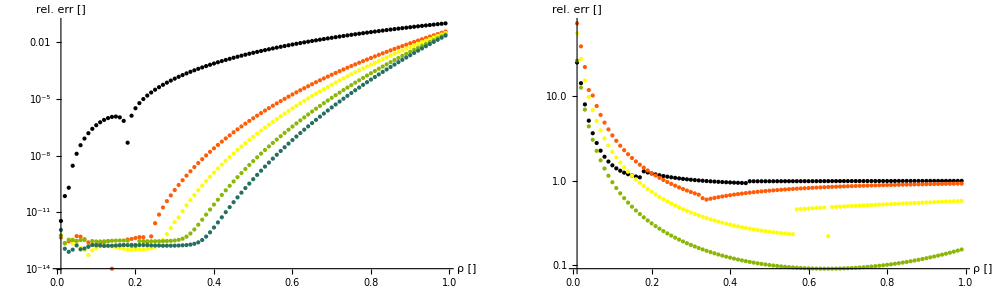

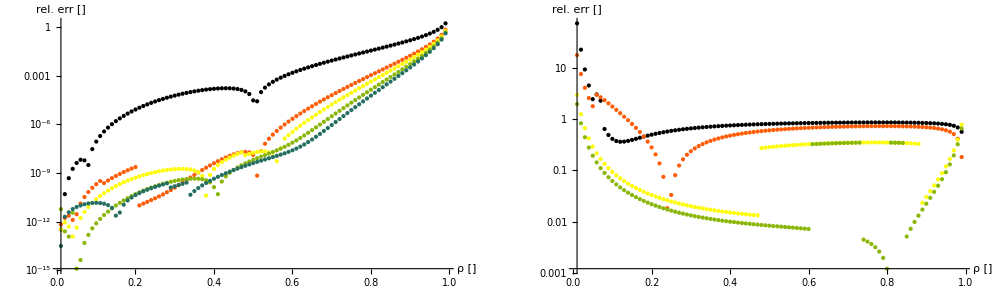

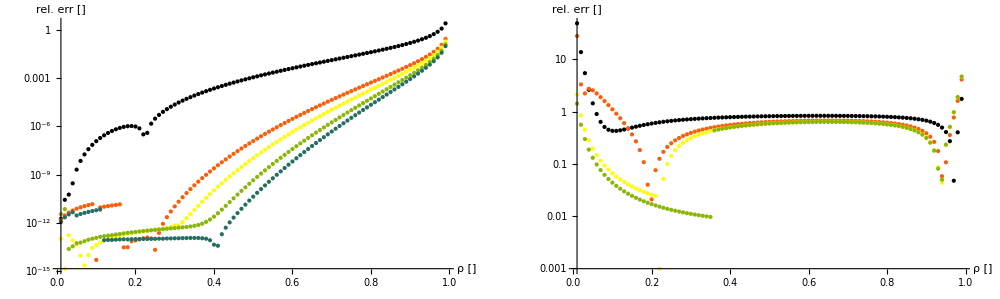

```mathematica
Show[GraphicsRow[{getCutBetaInv[0,Table[n↦Evaluate@If[Abs[n] > p,0,1],{p,{5,15,18,22,25}}]],getCutBetaInv[0,Table[n↦Evaluate@Exp[-(Abs[n])^2/(2p^2)],{p,{1,2,3,5}}]]}],ImageSize-> 1000]
Show[GraphicsRow[{getCutBetaInv[1,Table[n↦Evaluate@If[Abs[n] > p,0,1],{p,{5,15,18,22,25}}]],getCutBetaInv[1,Table[n↦Evaluate@Exp[-(Abs[n])^2/(2p^2)],{p,{2,5,13,16}}]]}],ImageSize-> 1000]
Show[GraphicsRow[{getCutBetaInv[2,Table[n↦Evaluate@If[Abs[n] > p,0,1],{p,{5,15,18,22,25}}]],getCutBetaInv[2,Table[n↦Evaluate@Exp[-(Abs[n])^2/(2p^2)],{p,{2,5,13,16}}]]}],ImageSize-> 1000]
```

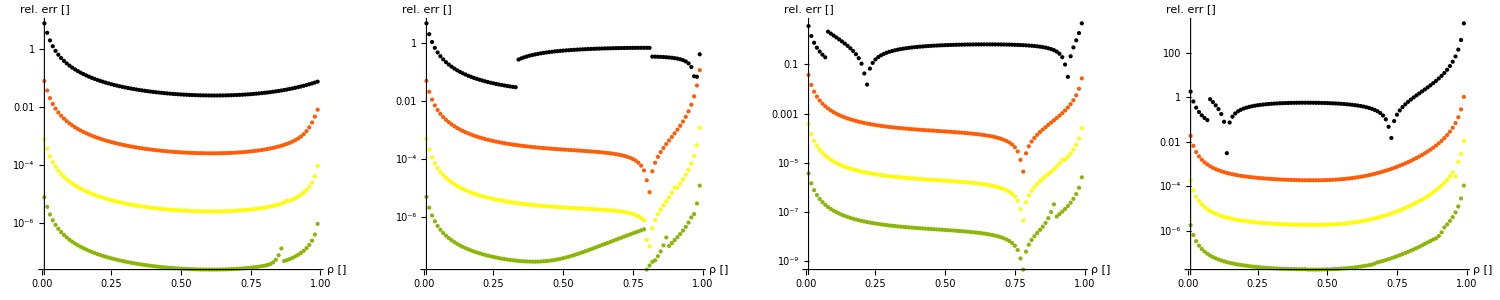

```mathematica
Show[GraphicsRow[Table[getCutBetaInv[v,Table[n↦Evaluate@Exp[-(Abs[n])^2/(2p^2)],{p,{10,100,1000,10000}}]],{v,{0,1,2,5}}]],ImageSize-> 1500]
```

```mathematica
getInvBeta[v_,invs_List]:=Module[{fN,fρ,ρs,lf,lNums,lErrs,path,ϵ,jac},
fN=n↦Beta[n,v/2+1];
fρ=ρ↦(ρ2β@ρ)^v;
ρs=Table[j,{j,.01,.99,.01}];
lf=Parallelize@Table[fρ[ρ],{ρ,ρs}];
lNums=(inv↦Parallelize@Table[inv[fN][ρ],{ρ,ρs}])/@invs;
lErrs = (l↦(Re@l - lf)/lf)/@lNums;
ListLogPlot[Evaluate@Parallelize[(l↦Transpose[{ρs,Abs@l}])/@lErrs],AxesLabel->{"ρ []","rel. err []"},PlotStyle->ColorData[3,"ColorList"]]
]
```

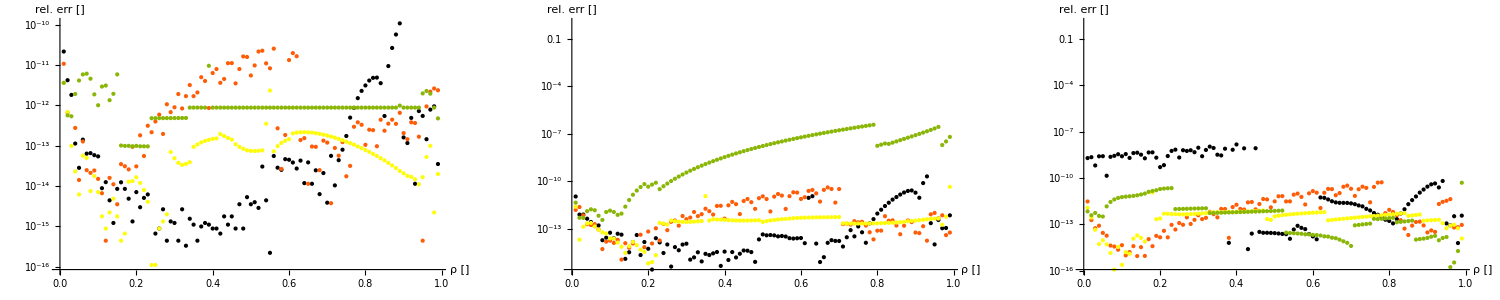

```mathematica
Show[GraphicsRow[Table[getInvBeta[v,{
fN↦getInvMellinTrafo[fN,2.7,1*^-8],
fN↦getInvMellinTrafo[fN,2.7,1*^-5],
fN↦getInvMellinTrafo[fN,2.7,1*^-2],
fN↦getInvMellinTrafo[fN,2.7,1]
}],{v,{0,1,2}}]],ImageSize-> 1500]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.994987  - 4.54747×10^-13\ ⅈ
 and 0.000331662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.969536  + 0.\ ⅈ
 and 3.10493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.98995  + 0.\ ⅈ
 and 0.0000610111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.964365  + 3.55271×10^-15\ ⅈ
 and 1.43883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.984886  - 3.55271×10^-15\ ⅈ
 and 0.0000214141 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.959166  + 0.\ ⅈ
 and 1.45416×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.1  - 8.67362×10^-18\ ⅈ
 and 1.7604×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.994987  + 1.36424×10^-12\ ⅈ
 and 0.000331662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.969536  + 0.\ ⅈ
 and 3.10493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.98995  + 0.\ ⅈ
 and 0.0000610111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.964365  + 3.55271×10^-15\ ⅈ
 and 1.43883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.984886  - 3.55271×10^-15\ ⅈ
 and 0.0000214141 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.959166  + 0.\ ⅈ
 and 1.45416×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.1  + 5.20417×10^-18\ ⅈ
 and 1.7604×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.994987  + 4.54747×10^-13\ ⅈ
 and 0.000331662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.969536  + 0.\ ⅈ
 and 3.10493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.98995  - 1.13687×10^-13\ ⅈ
 and 0.0000610111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.964365  + 3.55271×10^-15\ ⅈ
 and 1.43883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.984886  - 3.55271×10^-15\ ⅈ
 and 0.0000214141 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.959166  + 0.\ ⅈ
 and 1.45416×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.1  - 8.67362×10^-18\ ⅈ
 and 1.7604×10^-7 for the integral and error estimates.

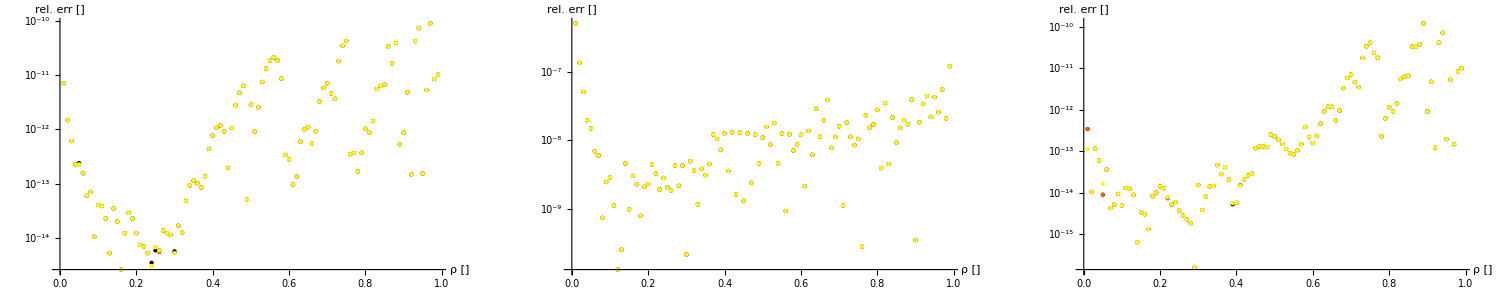

```mathematica
Module[{invs,path,ϵ,jac},
invs={};
ϵ=1*^-5;
path[y_]=2.7+(I-Sign[y]ϵ)y;
jac[y_] = (I-Sign[y] ϵ);
AppendTo[invs,
fN↦Evaluate@(ρ↦NIntegrate[jac[y]/(2π I)*(ρ^(-n)*fN[n])//.{n-> path[y]},{y,-∞,∞}])
];
ϵ=1*^-2;
AppendTo[invs,
fN↦Evaluate@(ρ↦NIntegrate[jac[y]/(2π I)*(ρ^(-n)*fN[n])//.{n-> path[y]},{y,-∞,∞}])
];
ϵ=1;
AppendTo[invs,
fN↦Evaluate@(ρ↦NIntegrate[jac[y]/(2π I)*(ρ^(-n)*fN[n])//.{n-> path[y]},{y,-∞,∞}])
];
Show[GraphicsRow[Table[getInvBeta[v,invs],{v,{0,1,2}}]],ImageSize-> 1500]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 1.  - 5.11917×10^-7\ ⅈ
 and 1.5774×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 1.  + 2.25514×10^-17\ ⅈ
 and 1.04391×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 1.  - 5.50682×10^-7\ ⅈ
 and 3.36444×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.969536  + 0.\ ⅈ
 and 3.10493×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.994987  - 4.54747×10^-13\ ⅈ
 and 0.000331662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.98995  + 1.13687×10^-13\ ⅈ
 and 0.0000610111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.964365  + 3.55271×10^-15\ ⅈ
 and 1.43883×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.984886  - 3.55271×10^-15\ ⅈ
 and 0.0000214141 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.959166  + 0.\ ⅈ
 and 1.45416×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-4.81037×10^7}. NIntegrate obtained 0.1  + 4.33681×10^-19\ ⅈ
 and 1.7604×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {4.81037×10^7}. NIntegrate obtained 0.1  - 1.47451×10^-17\ ⅈ
 and 3.29067×10^-7 for the integral and error estimates.

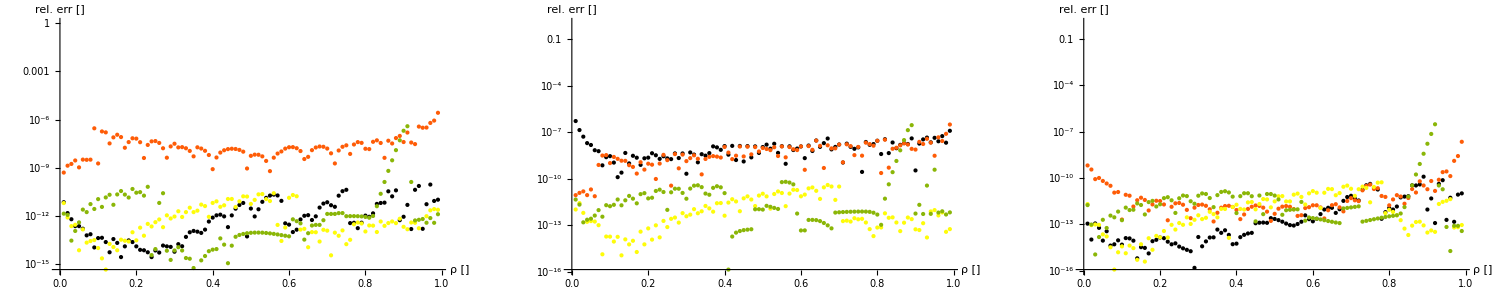

```mathematica
Module[{invs},
invs={};
AppendTo[invs,
fN↦Evaluate@(ρ↦NIntegrate[(I-Sign[y] 1*^-5)/(2π I)*(ρ^(-n)*fN[n])//.{n-> 2.7+(I-Sign[y]1*^-5)y},{y,-∞,∞}])
];
AppendTo[invs,
fN↦Evaluate@(ρ↦NIntegrate[(I-2y 1*^-5)/(2π I)*(ρ^(-n)*fN[n])//.{n-> 2.7+(I-y 1*^-5)y},{y,-∞,∞}])
];
AppendTo[invs,
fN↦Evaluate@(ρ↦NIntegrate[(I-4y^3 1*^-5)/(2π I)*(ρ^(-n)*fN[n])//.{n-> 2.7+(I-y^3 1*^-5)y},{y,-∞,∞}])
];
AppendTo[invs,
fN↦Evaluate@(ρ↦NIntegrate[(I-6y^5 1*^-5)/(2π I)*(ρ^(-n)*fN[n])//.{n-> 2.7+(I-y^5 1*^-5)y},{y,-∞,∞}])
];
Show[GraphicsRow[Table[getInvBeta[v,invs],{v,{0,1,2}}]],ImageSize-> 1500]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {14.5189}. NIntegrate obtained 0.5 and 1.54343×10^-6 for the integral and error estimates.

NIntegrate::inumr: The integrand Im[0.01`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.060000000000000005`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.11`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.16`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.2`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.24000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.28`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.32`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.02`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.06999999999999999`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.12`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.17`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.21000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.25`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.29000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.33`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.03`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.08`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.13`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.18000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.22`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.26`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.3`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.34`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.36000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.4`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.44`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.48000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.52`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.56`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.6`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.64`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.37`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.41000000000000003`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.45`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.49`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.53`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5700000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.61`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.65`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.38`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.42000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.46`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.54`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5800000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.62`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.66`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.68`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.72`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.76`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8400000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.88`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.92`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9600000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.6900000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.73`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.77`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.81`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.85`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.89`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.93`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.97`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.7000000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.74`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.78`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8200000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.86`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9400000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.98`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.01`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.02`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.03`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.01`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.02`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.03`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 1]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.01`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.060000000000000005`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.11`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.16`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.2`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.24000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.28`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.32`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.02`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.06999999999999999`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.12`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.17`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.21000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.25`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.29000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.33`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.03`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.08`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.13`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.18000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.22`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.26`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.3`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.34`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.36000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.4`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.44`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.48000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.52`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.56`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.6`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.64`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.37`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.41000000000000003`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.45`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.49`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.53`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5700000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.61`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.65`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.38`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.42000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.46`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.54`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5800000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.62`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.66`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.68`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.72`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.76`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8400000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.88`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.92`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9600000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.6900000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.73`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.77`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.81`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.85`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.89`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.93`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.97`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.7000000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.74`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.78`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8200000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.86`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9400000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.98`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.01`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.02`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.03`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 3/2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.01`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.060000000000000005`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.11`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.16`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.2`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.24000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.28`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.32`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.02`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.06999999999999999`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.12`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.17`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.21000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.25`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.29000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.33`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.03`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.08`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.13`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.18000000000000002`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.22`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.26`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.3`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.34`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.4`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.44`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.48000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.52`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.56`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.6`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.64`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.36000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.41000000000000003`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.45`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.49`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.53`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5700000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.61`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.65`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.37`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.42000000000000004`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.46`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.54`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.5800000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.62`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.66`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.38`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.72`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.76`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8400000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.88`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.92`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9600000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.68`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.73`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.77`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.81`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.85`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.89`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.93`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.97`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.6900000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.74`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.78`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.8200000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.86`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.9400000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.98`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.7000000000000001`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand Im[0.01`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.02`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand Im[0.03`^-2.7` - y (ⅈ + Times[« 2 »]) (ⅈ - 3 y^5/50000) Beta[2.7`  + y (ⅈ + Times[« 2 »]), 2]] InterpretationBox[Cell[
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

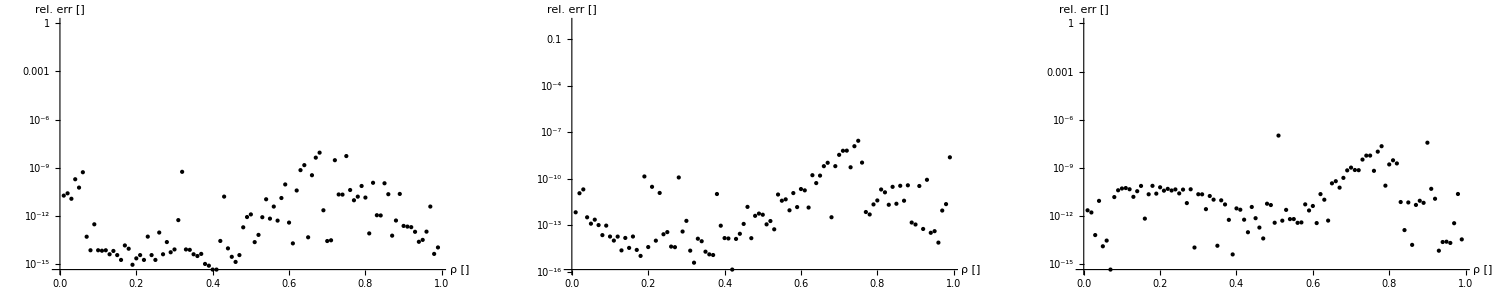

```mathematica
Module[{invs},
invs={};
(*AppendTo[invs,
fN↦Evaluate@(ρ↦2*NIntegrate[Re[(I-Sign[y] 1*^-5)/(2π I)*(ρ^(-n)*fN[n])//.{n-> 2.7+(I-Sign[y]1*^-5)y}],{y,0,∞}])
];
AppendTo[invs,
fN↦Evaluate@(ρ↦2*NIntegrate[Re[(I-2y 1*^-5)/(2π I)*(ρ^(-n)*fN[n])//.{n-> 2.7+(I-y 1*^-5)y}],{y,0,∞}])
];*)
AppendTo[invs,
fN↦Evaluate@(ρ↦2*NIntegrate[Re[(I-4y^3 1*^-5)/(2π I)*(ρ^(-n)*fN[n])//.{n-> 2.7+(I-y^3 1*^-5)y}],{y,0,∞}])
];
AppendTo[invs,
fN↦Evaluate@(ρ↦2*NIntegrate[Re[(I-6y^5 1*^-5)/(2π I)*(ρ^(-n)*fN[n])//.{n-> 2.7+(I-y^5 1*^-5)y}],{y,0,∞}])
];
Show[GraphicsRow[Table[getInvBeta[v,invs],{v,{0,1,2}}]],ImageSize-> 1500]
]
```

```mathematica
Options[getCutInv]={"toN"-> {}};
getCutInv[v_,gNs_List,opts:OptionsPattern[]]:=Module[{cMP,fN,fρ,hNs,hρ,ρs,lh,lf},
cMP=2.7;
fN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]}//.toN[OptionValue["toN"]])];
fρ=ρ↦(ρ2β@ρ)^v;
ρs=Table[j,{j,.01,.99,.01}];
lf=Parallelize@Table[fρ[ρ],{ρ,ρs}];
hNs = (n↦fN[n]*#[n])&/@gNs;
lh=(hN↦Parallelize@Table[getInvMellinTrafo[hN][ρ],{ρ,ρs}])/@hNs;
ListLogPlot[Evaluate@Parallelize[(l↦Transpose[{ρs,Abs[(Re@l-Re@lf)/Re@lf]}])/@lh],AxesLabel->{"ρ []","rel. err []"},PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
]
```

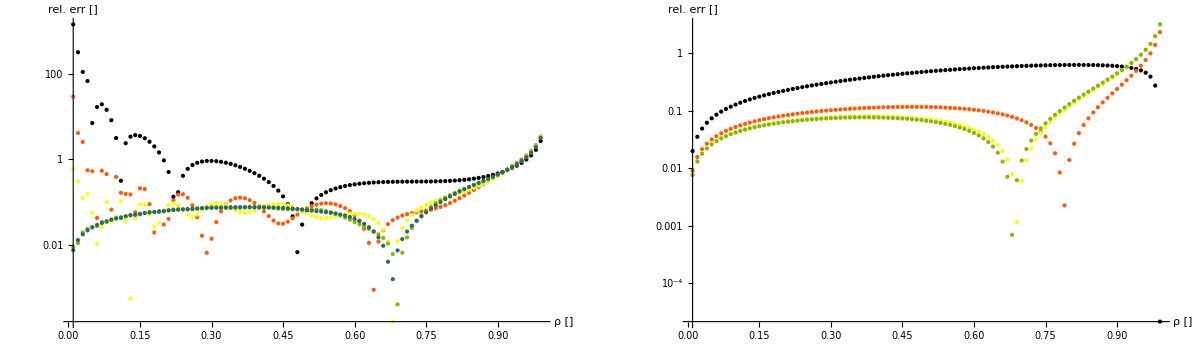

```mathematica
Show[GraphicsRow[{getCutInv[1,Table[n↦Evaluate@If[Abs[n] > p,0,1],{p,{5,15,18,22,25}}]],getCutInv[1,Table[n↦Evaluate@Exp[-(Abs[n])^2/(2p^2)],{p,{2,5,15,40}}]]}],ImageSize-> 1200]
```

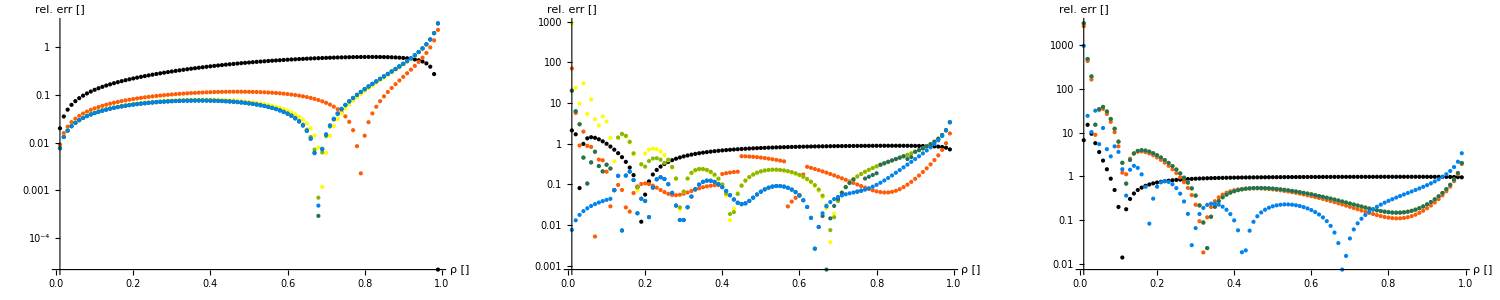

```mathematica
Show[GraphicsRow[{
getCutInv[1,Table[n↦Evaluate@Exp[-(Abs[n])^2/(2p^2)],{p,{2,5,15,40,100,1000}}]],
getCutInv[1,Table[n↦Evaluate@Exp[-(Abs[n])^4/(2p^4)],{p,{2,5,15,40,100,1000}}]],
getCutInv[1,Table[n↦Evaluate@Exp[-(Abs[n])^6/(2p^6)],{p,{2,5,15,40,100,1000}}]]
}],ImageSize-> 1500]
```

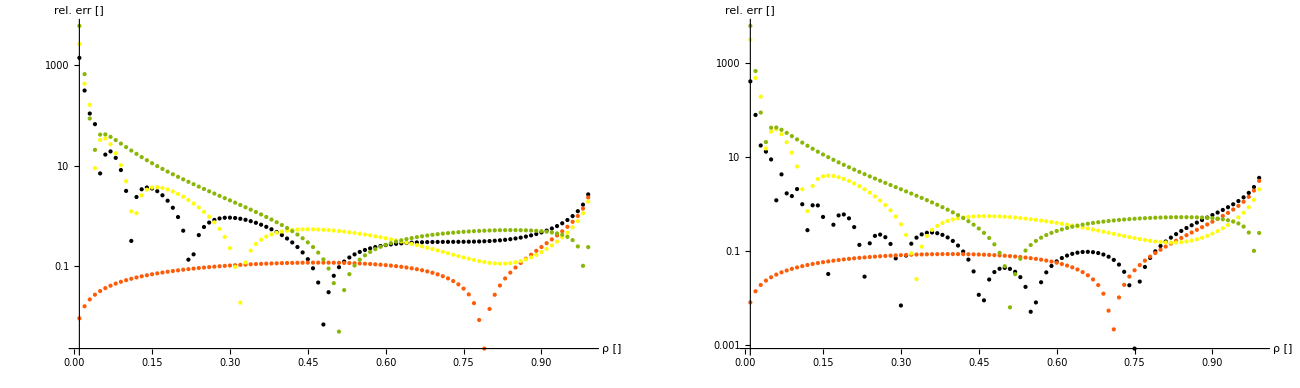

```mathematica
Show[GraphicsRow[{getCutInv[1,{
n↦Evaluate@If[Abs[n] > 5,0,1],
n↦Evaluate@Exp[-(Abs[n])^2/(2*5^2)],
n↦Evaluate@Exp[-(Abs[n])^6/(2*5^6)],
n↦Evaluate@Exp[-(Abs[n])^10/(2*5^10)]
}], getCutInv[1,{
n↦Evaluate@If[Abs[n] > 10,0,1],
n↦Evaluate@Exp[-(Abs[n])^2/(2*10^2)],
n↦Evaluate@Exp[-(Abs[n])^6/(2*10^6)],
n↦Evaluate@Exp[-(Abs[n])^10/(2*10^10)]
}]
}],ImageSize-> 1300]
```

{{1393.68-1.59162×10^-12 ⅈ,-308.623-3.41061×10^-13 ⅈ,108.197-3.33955×10^-13 ⅈ,66.4545-8.52651×10^-14 ⅈ,7.77357-2.84217×10^-14 ⅈ,-15.0725+3.55271×10^-14 ⅈ,-17.5051-4.26326×10^-14 ⅈ,-12.7002+1.77636×10^-15 ⅈ,-6.81337-1.24345×10^-14 ⅈ,-2.0198+2.22045×10^-15 ⅈ,1.24101-8.88178×10^-15 ⅈ,3.15756-5.32907×10^-15 ⅈ,4.07518-4.66294×10^-15 ⅈ,4.32043+0. ⅈ,4.15031-1.33227×10^-15 ⅈ,3.74949-3.41949×10^-14 ⅈ,3.24275+1.9984×10^-14 ⅈ,2.71001+2.30926×10^-14 ⅈ,2.19946+1.64313×10^-14 ⅈ,1.73766+1.15463×10^-14 ⅈ,1.33707+1.73195×10^-14 ⅈ,1.00116+1.33227×10^-15 ⅈ,0.728024+1.46549×10^-14 ⅈ,0.51274+2.19824×10^-14 ⅈ,0.348907-3.10862×10^-15 ⅈ,0.229625-3.10862×10^-15 ⅈ,0.148083+2.22045×10^-15 ⅈ,0.097903+2.22045×10^-15 ⅈ,0.0733075+3.33067×10^-16 ⅈ,0.0691943-2.22045×10^-16 ⅈ,0.0811393-1.15463×10^-14 ⅈ,0.105364+8.43769×10^-15 ⅈ,0.138684+1.68754×10^-14 ⅈ,0.178445-6.21725×10^-15 ⅈ,0.222462+1.46549×10^-14 ⅈ,0.268952+1.86517×10^-14 ⅈ,0.316482+1.64313×10^-14 ⅈ,0.363915-4.79616×10^-14 ⅈ,0.41036+1.33227×10^-15 ⅈ,0.455135-2.08722×10^-14 ⅈ,0.49773+1.11022×10^-14 ⅈ,0.537779+1.5099×10^-14 ⅈ,0.575031-2.4869×10^-14 ⅈ,0.609328-2.04281×10^-14 ⅈ,0.640591-4.21885×10^-14 ⅈ,0.668799-2.30926×10^-14 ⅈ,0.69398+2.66454×10^-15 ⅈ,0.716197+2.66454×10^-15 ⅈ,0.735545+6.21725×10^-15 ⅈ,0.752134+9.68114×10^-14 ⅈ,0.766094-2.04281×10^-14 ⅈ,0.777563-6.21725×10^-15 ⅈ,0.786683-3.28626×10^-14 ⅈ,0.793602+7.10543×10^-14 ⅈ,0.798467-1.59872×10^-14 ⅈ,0.801423+5.41789×10^-14 ⅈ,0.802613-1.24345×10^-14 ⅈ,0.802176+1.42109×10^-14 ⅈ,0.800244-5.24025×10^-14 ⅈ,0.796946+2.66454×10^-14 ⅈ,0.792404-2.13163×10^-14 ⅈ,0.786732+0. ⅈ,0.78004-5.9508×10^-14 ⅈ,0.77243+3.64153×10^-14 ⅈ,0.763999-4.26326×10^-14 ⅈ,0.754837+1.57208×10^-13 ⅈ,0.745028+2.13163×10^-14 ⅈ,0.73465+3.19744×10^-14 ⅈ,0.723777-7.01661×10^-14 ⅈ,0.712475+7.90479×10^-14 ⅈ,0.700806-3.81917×10^-14 ⅈ,0.688829+4.70735×10^-14 ⅈ,0.676596-8.79297×10^-14 ⅈ,0.664155+7.28306×10^-14 ⅈ,0.651552-1.36779×10^-13 ⅈ,0.638828+1.06581×10^-13 ⅈ,0.626018-5.32907×10^-14 ⅈ,0.613158-1.42109×10^-14 ⅈ,0.600279+9.59233×10^-14 ⅈ,0.587408+9.76996×10^-14 ⅈ,0.574571-3.73035×10^-14 ⅈ,0.561791-1.54543×10^-13 ⅈ,0.549088+1.36779×10^-13 ⅈ,0.536481+1.01252×10^-13 ⅈ,0.523986+3.19744×10^-14 ⅈ,0.511619+3.73035×10^-14 ⅈ,0.499391-4.44089×10^-14 ⅈ,0.487315+1.22569×10^-13 ⅈ,0.475401+2.55795×10^-13 ⅈ,0.463657+1.13687×10^-13 ⅈ,0.452091+1.47438×10^-13 ⅈ,0.440709-5.50671×10^-14 ⅈ,0.429518+3.73035×10^-14 ⅈ,0.41852+4.9738×10^-14 ⅈ,0.407721-1.82965×10^-13 ⅈ,0.397123+9.41469×10^-14 ⅈ,0.386728-2.66454×10^-14 ⅈ,0.376538-1.42109×10^-14 ⅈ,0.366553+1.77636×10^-14 ⅈ},{0.984362-1.81899×10^-12 ⅈ,0.971481-3.63798×10^-12 ⅈ,0.959604-1.04872×10^-12 ⅈ,0.948369+2.25685×10^-8 ⅈ,0.937607-2.23821×10^-13 ⅈ,0.927219-4.71945×10^-9 ⅈ,0.917139-1.15097×10^-9 ⅈ,0.907322+4.19081×10^-9 ⅈ,0.897733+6.03664×10^-9 ⅈ,0.888346+2.22933×10^-13 ⅈ,0.879139-1.27499×10^-9 ⅈ,0.870095+3.82618×10^-11 ⅈ,0.861201-2.12754×10^-9 ⅈ,0.852443-1.24834×10^-9 ⅈ,0.843811-2.54019×10^-13 ⅈ,0.835297-8.28893×10^-10 ⅈ,0.826893-3.25111×10^-10 ⅈ,0.818591-1.9397×10^-9 ⅈ,0.810386+9.43753×10^-10 ⅈ,0.802272-1.29341×10^-14 ⅈ,0.794244+5.72689×10^-10 ⅈ,0.786298+3.91724×10^-10 ⅈ,0.77843+5.59394×10^-11 ⅈ,0.770635+4.00846×10^-10 ⅈ,0.762912+0. ⅈ,0.755255-5.68872×10^-10 ⅈ,0.747664-1.95335×10^-10 ⅈ,0.740134-4.28693×10^-10 ⅈ,0.732664+0. ⅈ,0.725251-5.23453×10^-16 ⅈ,0.717893-2.6381×10^-10 ⅈ,0.710589-1.82671×10^-10 ⅈ,0.703336-3.10761×10^-10 ⅈ,0.696132-2.6741×10^-10 ⅈ,0.688976-1.19721×10^-13 ⅈ,0.681867-4.58048×10^-14 ⅈ,0.674802+1.48133×10^-10 ⅈ,0.667781+1.49459×10^-10 ⅈ,0.6608+1.39989×10^-10 ⅈ,0.653859-1.04083×10^-15 ⅈ,0.646956+1.79033×10^-10 ⅈ,0.640089+2.06194×10^-10 ⅈ,0.633256+1.93294×10^-10 ⅈ,0.626455+2.41676×10^-10 ⅈ,0.619682-2.5502×10^-14 ⅈ,0.612937+1.62456×10^-10 ⅈ,0.606216+7.75887×10^-7 ⅈ,0.599516+7.4807×10^-7 ⅈ,0.592834+6.48246×10^-7 ⅈ,0.586169+5.60801×10^-14 ⅈ,0.579515+1.60857×10^-10 ⅈ,0.572871-5.17312×10^-11 ⅈ,0.566232+5.37597×10^-11 ⅈ,0.559597-2.28401×10^-11 ⅈ,0.55296+1.05118×10^-14 ⅈ,0.546321-7.70459×10^-11 ⅈ,0.539674-4.58015×10^-11 ⅈ,0.533018+2.77556×10^-17 ⅈ,0.52635-1.20971×10^-10 ⅈ,0.519667-6.87599×10^-15 ⅈ,0.512967-3.62841×10^-7 ⅈ,0.506247-2.6241×10^-7 ⅈ,0.499507-1.53206×10^-7 ⅈ,0.492745-4.28095×10^-8 ⅈ,0.485959+6.23238×10^-8 ⅈ,0.479149+1.56397×10^-7 ⅈ,0.472315+2.35657×10^-7 ⅈ,0.465456+2.97056×10^-7 ⅈ,0.458572+3.39113×10^-7 ⅈ,0.451665-4.16334×10^-17 ⅈ,0.444736-5.35556×10^-11 ⅈ,0.437785-5.26565×10^-11 ⅈ,0.430814-1.2863×10^-11 ⅈ,0.423827+1.11463×10^-11 ⅈ,0.416823+0. ⅈ,0.409808+9.93155×10^-12 ⅈ,0.402783+3.1333×10^-11 ⅈ,0.395751+4.72857×10^-8 ⅈ,0.388716+1.29828×10^-8 ⅈ,0.381681-6.91761×10^-8 ⅈ,0.37465-1.19421×10^-7 ⅈ,0.367627+1.62536×10^-7 ⅈ,0.360616-1.97215×10^-7 ⅈ,0.35362-2.23067×10^-7 ⅈ,0.346645+5.61789×10^-16 ⅈ,0.339694+2.47869×10^-7 ⅈ,0.332771+5.79042×10^-11 ⅈ,0.32588+7.01128×10^-11 ⅈ,0.319027+3.25269×10^-11 ⅈ,0.312214-2.45567×10^-14 ⅈ,0.305447+5.83299×10^-11 ⅈ,0.298728+5.34825×10^-11 ⅈ,0.292063-1.12504×10^-7 ⅈ,0.285454+7.84372×10^-8 ⅈ,0.278906-3.8181×10^-15 ⅈ,0.272422-9.7893×10^-9 ⅈ,0.266005-2.26909×10^-8 ⅈ,0.259659-5.30311×10^-8 ⅈ,0.253387+8.05873×10^-8 ⅈ},{2276.2+0. ⅈ,-379.784-1.13687×10^-13 ⅈ,-134.648-3.41061×10^-13 ⅈ,-2.72742+0. ⅈ,30.8062+0. ⅈ,31.2193+0. ⅈ,23.4467+0. ⅈ,15.359+0. ⅈ,8.96924+0. ⅈ,4.43899+0. ⅈ,1.43255+0. ⅈ,-0.44735+0. ⅈ,-1.53638+0. ⅈ,-2.08859-1.95399×10^-14 ⅈ,-2.28674+0. ⅈ,-2.25874+0. ⅈ,-2.09248+0. ⅈ,-1.84749+0. ⅈ,-1.56348+0. ⅈ,-1.26649+0. ⅈ,-0.973131+0. ⅈ,-0.693623+0. ⅈ,-0.433854+0. ⅈ,-0.196814-6.66134×10^-16 ⅈ,0.0164156+0. ⅈ,0.205984+0. ⅈ,0.372807+0. ⅈ,0.518252+0. ⅈ,0.643922+0. ⅈ,0.751519+0. ⅈ,0.84275-4.9627×10^-14 ⅈ,0.919268-4.59632×10^-14 ⅈ,0.982636+0. ⅈ,1.03431+0. ⅈ,1.07563+0. ⅈ,1.10782+0. ⅈ,1.13198+0. ⅈ,1.14912+0. ⅈ,1.16011+0. ⅈ,1.16577+0. ⅈ,1.16679+0. ⅈ,1.16382+0. ⅈ,1.15742+0. ⅈ,1.14807+0. ⅈ,1.13621-9.44245×10^-14 ⅈ,1.12224-5.55389×10^-14 ⅈ,1.10649-2.43694×10^-14 ⅈ,1.08927+3.60822×10^-16 ⅈ,1.07083+1.99701×10^-14 ⅈ,1.05141+3.52912×10^-14 ⅈ,1.0312+4.68653×10^-14 ⅈ,1.0104+0. ⅈ,0.989139+0. ⅈ,0.967567+0. ⅈ,0.945796+0. ⅈ,0.923929+0. ⅈ,0.902052+0. ⅈ,0.880241+0. ⅈ,0.858562+0. ⅈ,0.837068+0. ⅈ,0.815809+0. ⅈ,0.794823+0. ⅈ,0.774143+0. ⅈ,0.753798+0. ⅈ,0.73381+0. ⅈ,0.714197+0. ⅈ,0.694974+0. ⅈ,0.676152+0. ⅈ,0.65774+0. ⅈ,0.639742+0. ⅈ,0.622163+0. ⅈ,0.605004+0. ⅈ,0.588265+0. ⅈ,0.571944+0. ⅈ,0.556039+0. ⅈ,0.540545+0. ⅈ,0.525459+0. ⅈ,0.510774+0. ⅈ,0.496485+0. ⅈ,0.482584+0. ⅈ,0.469065+0. ⅈ,0.455921+0. ⅈ,0.443143+0. ⅈ,0.430724+0. ⅈ,0.418656+0. ⅈ,0.291589-0.0234349 ⅈ,0.2832-0.0203103 ⅈ,0.275082-0.0173753 ⅈ,0.267226-0.0146193 ⅈ,0.259623-0.0120321 ⅈ,0.252263-0.00960426 ⅈ,0.245139-0.00732682 ⅈ,0.238241-0.00519134 ⅈ,0.231562-0.00318985 ⅈ,0.225095-0.00131485 ⅈ,0.218832+0.000440745 ⅈ,0.212766+0.00208361 ⅈ,0.20689+0.00362005 ⅈ,0.201197+0.00505602 ⅈ},{-6035.14+0. ⅈ,-654.322+0. ⅈ,-83.9212+0. ⅈ,21.2468+0. ⅈ,41.3343+0. ⅈ,41.5206+3.55271×10^-13 ⅈ,36.9805+3.2685×10^-13 ⅈ,31.7956+0. ⅈ,27.0778+0. ⅈ,23.0622+0. ⅈ,19.721+0. ⅈ,16.9584+0. ⅈ,14.6719+0. ⅈ,12.7716+0. ⅈ,11.1834+0. ⅈ,9.84785+0. ⅈ,8.71757+0. ⅈ,7.75509+0. ⅈ,6.93058+0. ⅈ,6.22025+0. ⅈ,5.60498+0. ⅈ,5.06933+0. ⅈ,4.60078+0. ⅈ,4.18906+0. ⅈ,3.82577+0. ⅈ,3.50391+0. ⅈ,3.21771+0. ⅈ,2.96231+0. ⅈ,2.73363+0. ⅈ,2.52824+0. ⅈ,2.34322+0. ⅈ,2.17607+0. ⅈ,2.02467+0. ⅈ,1.88719+0. ⅈ,1.76204+0. ⅈ,1.64786+0. ⅈ,1.54346+0. ⅈ,1.4478+0. ⅈ,1.35998+0. ⅈ,1.27921+0. ⅈ,1.20478+0. ⅈ,1.13607+0. ⅈ,1.07255+0. ⅈ,1.01372+1.23235×10^-14 ⅈ,0.959161+4.30767×10^-14 ⅈ,0.908483+6.59195×10^-14 ⅈ,0.861345+8.28781×10^-14 ⅈ,0.817441+9.48686×10^-14 ⅈ,0.776496+1.02959×10^-13 ⅈ,0.738261+1.07941×10^-13 ⅈ,0.702515+1.10453×10^-13 ⅈ,0.669057+1.10939×10^-13 ⅈ,0.637704+1.0994×10^-13 ⅈ,0.608293+1.07858×10^-13 ⅈ,0.580674+1.04805×10^-13 ⅈ,0.554712+1.011×10^-13 ⅈ,0.530282+9.70196×10^-14 ⅈ,0.507274+0. ⅈ,0.485584+0. ⅈ,0.465119+0. ⅈ,0.445792+0. ⅈ,0.427525+0. ⅈ,0.410246+0. ⅈ,0.393889+0. ⅈ,0.378392+0. ⅈ,0.363699+0. ⅈ,0.349759+0. ⅈ,0.336523+0. ⅈ,0.323948+0. ⅈ,0.311993+0. ⅈ,0.300619+0. ⅈ,0.289791+0. ⅈ,0.279477+0. ⅈ,0.269647+0. ⅈ,0.260272+0. ⅈ,0.251327+0. ⅈ,0.242786+0. ⅈ,0.234627+0. ⅈ,0.22683+0. ⅈ,0.219373+0. ⅈ,0.212239+0. ⅈ,0.20541+0. ⅈ,0.19887+0. ⅈ,0.192604+0. ⅈ,0.186598+0. ⅈ,0.180837+0. ⅈ,0.175311+0. ⅈ,0.170006+0. ⅈ,0.164913+0. ⅈ,0.16002+0. ⅈ,0.155317+0. ⅈ,0.150796+0. ⅈ,0.146448+0. ⅈ,0.142264+0. ⅈ,0.138238+0. ⅈ,0.134361+0. ⅈ,0.130626+0. ⅈ,0.127028+0. ⅈ,0.123559+0. ⅈ}}

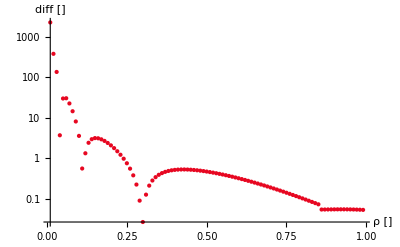

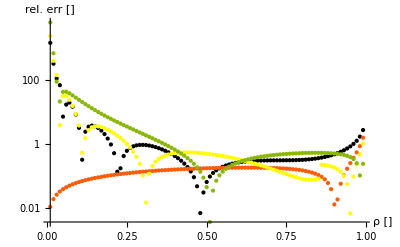

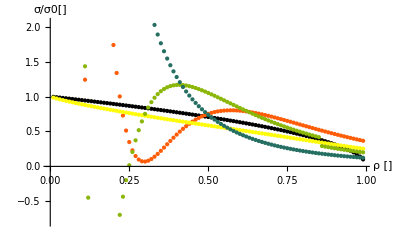

```mathematica
Module[{v,cMP,fN,fρ,p,gNs,hNs,hρ,ρs,lh,lf},
v=1;
cMP=2.7;
fN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]}//.toN[])];
fρ=ρ↦(ρ2β@ρ)^v;
ρs=Table[j,{j,.01,.99,.01}];
lf=Parallelize@Table[fρ[ρ],{ρ,ρs}]1;
p=5;
gNs = (*Table[n↦Evaluate@Exp[-(Abs[n])^2/(2p^2)],{p,{50,100,200}}];*){
n↦Evaluate@If[Abs[n] > p,0,1],
n↦Evaluate@Exp[-(Abs[n])^2/(p^2)],
n↦Evaluate@Exp[-(Abs[n])^6/(p^6)],
n↦Evaluate@Exp[-(Abs[n])^10/(p^10)]
};
hNs = (n↦fN[n]*#[n])&/@gNs;
lh=(hN↦Parallelize@Table[getInvMellinTrafo[hN][ρ],{ρ,ρs}])/@hNs;
Print@ListLogPlot[Evaluate[Transpose[{ρs,Abs[lh[[3]]-lh[[2]]]}]],AxesLabel->{"ρ []","diff []"},PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]];
Print@ListLogPlot[Evaluate@Parallelize[(l↦Transpose[{ρs,Abs[(Re@l-Re@lf)/Re@lf]}])/@lh],AxesLabel->{"ρ []","rel. err []"},PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]];
ListPlot[Evaluate@Join[{Transpose[{ρs,lf}]},Parallelize[(l↦Transpose[{ρs,Re@l}])/@lh]],AxesLabel->{"ρ []","σ/σ0[]"},PlotStyle->ColorData[3,"ColorList"]]
]
```

```mathematica
(*getLinearEnvelope[data_List]:=Module[{xs,ys,f,m,c,diff,sol},
(* seperate *)
{xs,ys} = Transpose[data];
f = x↦m*x+c;
diff=Table[f[d[[1]]]-d[[2]],{d,data}];
sol=FindFit[data,{f[x],Min[diff] ≥ 0},{m,c},x];
{m,c}/.sol
];*)
```

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
Options[getSplitLimits]={"toN"-> {}};
getSplitLimits[v_,orders_,opts:OptionsPattern[]]:=Module[{
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
xs,x2ρ,xLabel,lFull,lSer,toxPlot, lRelErrs, envs, y
},
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[OptionValue["toN"]],2.7,1];
serρs=(f↦getInvMellinTrafo[f//.toN[OptionValue["toN"]],2.7,1])/@serNs;
(* compute values on grid *)
(*xs = Table[j,{j,-2.5,0.5,.05}];
xLabel="ln(η) []";
x2ρ[x_]=η2ρ@Exp@x;*)
(*xs=Table[j,{j,-2,-.01,.03}];
xLabel = "ln(β) []";
x2ρ[x_]=β2ρ[10^x];*)
xs=Table[ρ,{ρ,0.01,0.45,.01}];
xLabel = "ρ []";
x2ρ[x_]=x;
lFull = Parallelize@Table[fullρ[x2ρ@x],{x,xs}];
lSer = (fρ↦Parallelize@Table[fρ[x2ρ@x],{x,xs}])/@serρs;
(* relative error *)
lRelErrs = Parallelize[(l↦Log10@Abs[(Re@l-Re@lFull)/Re@lFull])/@lSer];
(* compute envelopes *)
toxPlot[l_]:=Transpose[{xs,l}];
ListPlot[(l↦toxPlot@l)/@lRelErrs,AxesLabel-> {xLabel,"log10 rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
(*envs = Parallelize[(l↦getLinearEnvelope[toxPlot@l])/@lRelErrs];
(* Plot *)
GraphicsRow[{
Show[{
ListPlot[(l↦toxPlot@l)/@lRelErrs,AxesLabel-> {xLabel,"log10 rel. error []"},PlotStyle->ColorData[3,"ColorList"]],
Plot[Evaluate[(env↦env[[1]]*ln10η+env[[2]])/@envs],{ln10η,Min@xs,Max@xs},PlotStyle->ColorData[3,"ColorList"]]
}],
Plot[Evaluate[(env↦env[[1]]*ln10η+env[[2]])/@envs],{ln10η,Min@xs,Max@xs},AxesLabel-> {xLabel,"log10 rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
}]*)
(*y=-1;
GraphicsRow[{
Plot[Evaluate@Parallelize[(env↦env[[1]]*ln10η+env[[2]])/@envs],{ln10η,Min@Log10@ηs,Max@Log10@ηs},AxesLabel-> {"ln10(η) []","log10 rel. error []"},PlotStyle->ColorData[3,"ColorList"]],
ListPlot[Evaluate@Parallelize[(e↦{e[[1]],e[[2]][[1]]})/@Transpose[{orders,envs}]],AxesLabel-> {"order", "m"}],
ListPlot[Evaluate@Parallelize[(e↦{e[[1]],e[[2]][[2]]})/@Transpose[{orders,envs}]],AxesLabel-> {"order", "c"}],
ListPlot[Evaluate@Parallelize[(e↦{e[[1]],(y-e[[2]][[2]])/e[[2]][[1]]})/@Transpose[{orders,envs}]],AxesLabel-> {"order", "y=-1"}]
},Spacings->0]*)
];
```

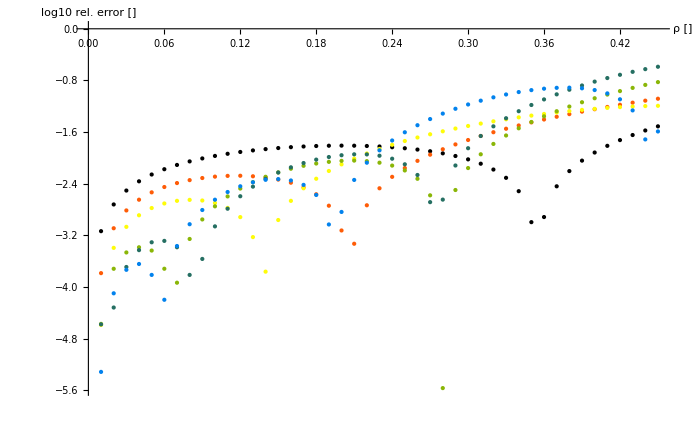

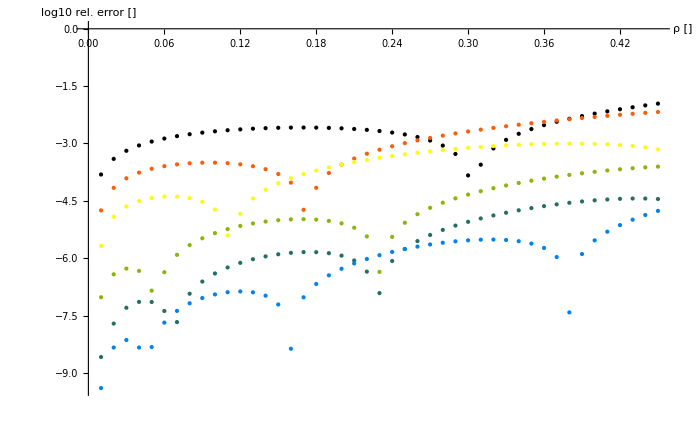

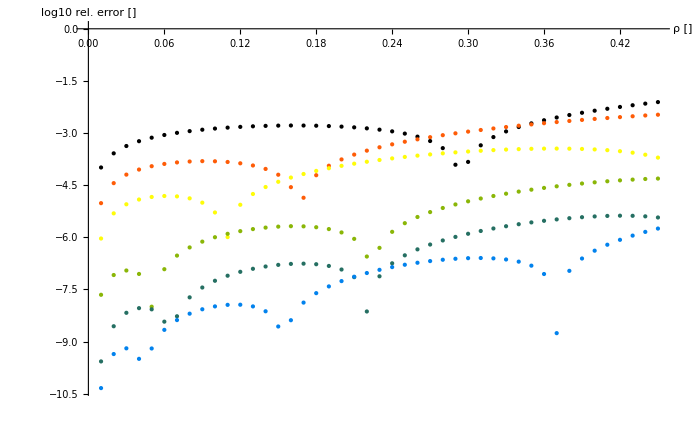

```mathematica
Show[getSplitLimits[1,{2,4, 6,10,13,15}],ImageSize->700]
Show[getSplitLimits[1,{2,4, 6,10,13,15},"toN"-> {"αμ"->.15}],ImageSize->700]
Show[getSplitLimits[1,{2,4, 6,10,13,15},"toN"-> {"αμ"->.12}],ImageSize->700]
```

-Graphics-

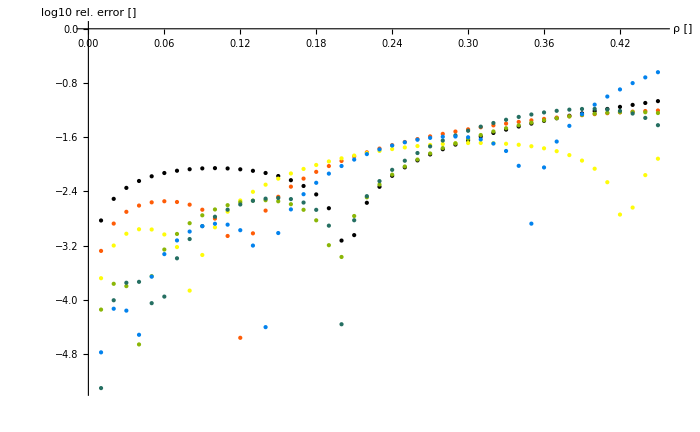

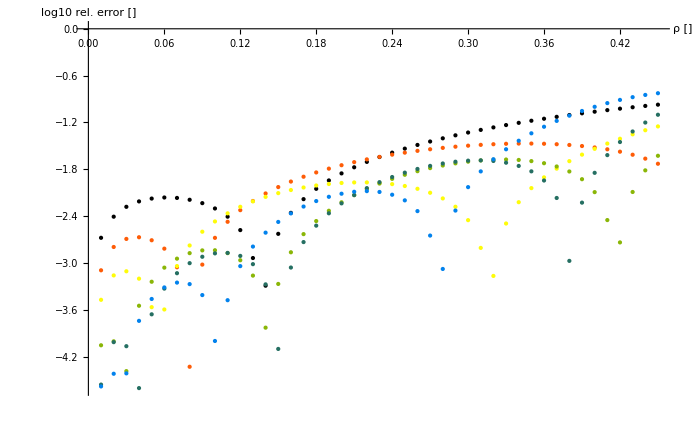

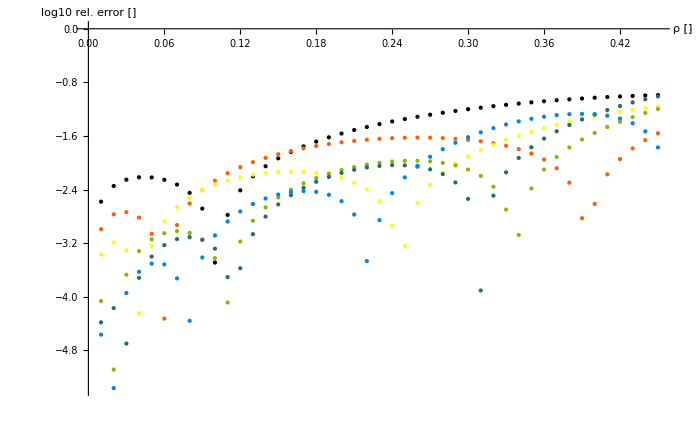

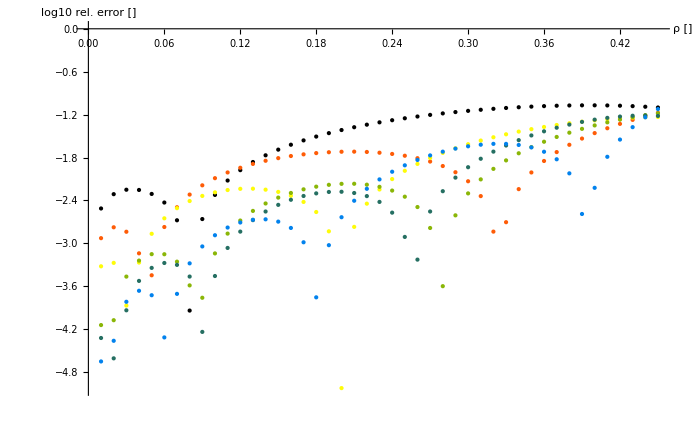

```mathematica
Do[Print@Show[getSplitLimits[v,{2,4, 6,10,13,15}],ImageSize->700],{v,{1,2,3,4,5}}]
```

{0.986707-1.7053×10^-13 ⅈ,0.975155+1.77636×10^-13 ⅈ,0.964359+0. ⅈ,0.95409-8.88178×10^-15 ⅈ,0.944237+0. ⅈ,0.934733+0. ⅈ,0.925535+4.26326×10^-14 ⅈ,0.916609+2.66454×10^-14 ⅈ,0.907934+9.33016×10^-13 ⅈ,0.89949-1.03616×10^-12 ⅈ,0.891262+1.14064×10^-12 ⅈ,0.88324-1.24551×10^-12 ⅈ,0.875414-4.21885×10^-15 ⅈ,0.867774-2.44249×10^-15 ⅈ,0.860316+6.58908×10^-12 ⅈ,0.853033+2.70155×10^-12 ⅈ,0.845919-1.77806×10^-11 ⅈ,0.838972-3.97152×10^-11 ⅈ,0.832188+0. ⅈ,0.825563+0. ⅈ,0.819095+0. ⅈ,0.812782+0. ⅈ,0.806622+0. ⅈ,0.800614-2.22045×10^-16 ⅈ,0.794756+0. ⅈ,0.789048-2.22045×10^-16 ⅈ,0.783489+0. ⅈ,0.778078+0. ⅈ,0.772815+0. ⅈ,0.767699+0. ⅈ,0.762732+0. ⅈ,0.757913+0. ⅈ,0.753242+0. ⅈ,0.74872+0. ⅈ,0.744347-1.11022×10^-16 ⅈ,0.740125+0. ⅈ,0.736055+0. ⅈ,0.732136+0. ⅈ,0.728371+0. ⅈ,0.724761+0. ⅈ,0.721308-1.11022×10^-16 ⅈ,0.718012+0. ⅈ,0.714875-1.11022×10^-16 ⅈ,0.7119+0. ⅈ,0.709089+0. ⅈ,0.706442+0. ⅈ,0.703964+0. ⅈ,0.701655+0. ⅈ,0.699519+5.55112×10^-17 ⅈ,0.697558+1.73472×10^-18 ⅈ,0.695775+0. ⅈ,0.694174-5.55112×10^-17 ⅈ,0.692756+0. ⅈ,0.691525-8.25728×10^-14 ⅈ,0.690486-8.28781×10^-14 ⅈ,0.689641+8.31557×10^-14 ⅈ,0.688994+8.33777×10^-14 ⅈ,0.688549+8.37386×10^-14 ⅈ,0.688311-8.40439×10^-14 ⅈ,0.688284-8.42659×10^-14 ⅈ,0.688473+8.46268×10^-14 ⅈ,0.688882+8.48766×10^-14 ⅈ,0.689517+8.51264×10^-14 ⅈ,0.690383+8.54594×10^-14 ⅈ,0.691486+0. ⅈ,0.692831+0. ⅈ,0.694425+0. ⅈ,0.696274+0. ⅈ,0.698385+8.68472×10^-14 ⅈ,0.700765+8.71525×10^-14 ⅈ,0.703422-8.74301×10^-14 ⅈ,0.706363-8.76937×10^-14 ⅈ,0.709596-8.79574×10^-14 ⅈ,0.71313+8.82489×10^-14 ⅈ,0.716973+8.84848×10^-14 ⅈ,0.721135+8.87901×10^-14 ⅈ,0.725623+8.90399×10^-14 ⅈ,0.730448+8.93174×10^-14 ⅈ,0.73562+8.96228×10^-14 ⅈ,0.741146-8.98726×10^-14 ⅈ,0.747037+0. ⅈ,0.7533+0. ⅈ,0.759943+0. ⅈ,0.766971+0. ⅈ,0.774388+0. ⅈ,0.782193-3.57686×10^-13 ⅈ,0.790379+3.77209×10^-13 ⅈ,0.798931+3.96277×10^-13 ⅈ,0.80782+0. ⅈ,0.816996+2.77556×10^-17 ⅈ,0.826377+0. ⅈ,0.835828+0. ⅈ,0.845127+0. ⅈ,0.853895-1.08159×10^-7 ⅈ,0.861465+1.22373×10^-7 ⅈ,0.866577+0. ⅈ,0.866601+0. ⅈ,0.855015-1.46147×10^-13 ⅈ,0.809169-1.33119×10^-10 ⅈ}

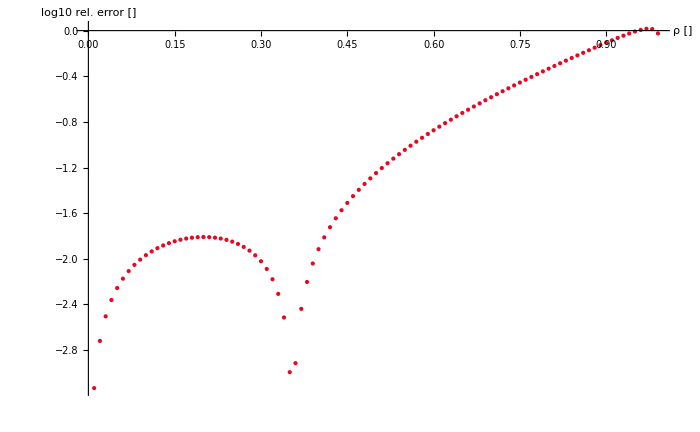

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
Options[getMellinOfOrder]={"toN"-> {}};
getMellinOfOrder[v_,order_,opts:OptionsPattern[]]:=Module[{
fullN,serΔLL,serN,fullρ,serρ,
xs,x2ρ,xLabel,lFull,lSer,toxPlot, lRelErr
},
(* get series *)
serΔLL = Normal@Series[ΔLL,{lnN,0,order}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serN =n↦Evaluate[Beta[n,v/2+1]*(serΔLL/.{lnN -> Log[n+1]})];
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[OptionValue["toN"]]];
serρ=getInvMellinTrafo[serN//.toN[OptionValue["toN"]],2.7,1];
(* compute values on grid *)
(*xs = Table[j,{j,-2.5,0.5,.05}];
xLabel="ln(η) []";
x2ρ[x_]=η2ρ@Exp@x;*)
(*xs=Table[j,{j,-2,-.01,.03}];
xLabel = "ln(β) []";
x2ρ[x_]=β2ρ[10^x];*)
xs=Table[ρ,{ρ,0.01,0.99,.01}];
xLabel = "ρ []";
x2ρ[x_]=x;
lFull = Parallelize@Table[fullρ[x2ρ@x],{x,xs}];
lSer = Parallelize@Table[serρ[x2ρ@x],{x,xs}];
Print@lSer;
(* relative error *)
lRelErr= Log10@Abs[(Re@lSer-Re@lFull)/Re@lFull];
toxPlot[l_]:=Transpose[{xs,l}];
ListPlot[toxPlot@lRelErr,AxesLabel-> {xLabel,"log10 rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
];
Show[getMellinOfOrder[1,2],ImageSize-> 700]
```